```mathematica
Trials for Good equation rescaling
This notebook is for comparing the good equation rescaling to the Ugly one, doing the same but only having different differential equation
```

equation for Good rescaling Trials

```mathematica
ClearAll["Global`*"]
```

## Compute geometric quantities

In this section we define the coordinates, metric, Christoffels and curvature. This is just geometry-- all in spherical polar coords.

Define coordinates

```mathematica
X={T,R,θ,ϕ};
```

Define 4-metric

```mathematica
g={{-1,0,0,0},{0,1,0,0},{0,0,R^2,0},{0,0,0,R^2 Sin[θ]^2}};g//MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | R^2 | 0
0 | 0 | 0 | R^2 Sin[θ]^2)

```mathematica
ginv=g//Inverse//Simplify;ginv//MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1/R^2 | 0
0 | 0 | 0 | Csc[θ]^2/R^2)

Compute Christoffels:

(Γ^γ)_αβ = 1/2 g^γζ(g_(αζ,β)+g_(ζβ,α)-g_(αβ,ζ))

```mathematica
Christoffelsudd = Table[1/2 Sum[ginv[[γ,ζ]](D[g[[ζ,β]], X[[α]]]+D[g[[α,ζ]], X[[β]]]-D[g[[α,β]], X[[ζ]]]),{ζ,4}],{γ,4},{α,4},{β,4}]//Simplify;
```

```mathematica
Table[Table[Christoffelsudd[[γ,α,β]],{γ,4}],{α,4},{β,4}]//MatrixForm
```

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
1/R
0) | (0
0
0
1/R)
(0
0
0
0) | (0
0
1/R
0) | (0
-R
0
0) | (0
0
0
Cot[θ])
(0
0
0
0) | (0
0
0
1/R) | (0
0
0
Cot[θ]) | (0
-R Sin[θ]^2
-Cos[θ] Sin[θ]
0))

Define Contracted Christoffels

Γ^a = g^μν (Γ^a)_μν ; Γ_a = g_ab Γ^b

```mathematica
ContractedChristoffelsu=Table[Sum[ginv[[a,b]]Christoffelsudd[[c,a,b]],{a,4},{b,4}],{c,4}]//Simplify
```

{0,-2/R,-Cot[θ]/R^2,0}

```mathematica
ContractedChristoffelsd=Table[Sum[g[[a,b]]ContractedChristoffelsu[[b]],{b,4}],{a,4}]//Simplify
```

{0,-2/R,-Cot[θ],0}

Riemann Christoffel Tensor:

(R^μ)_ναβ = ∂_α (Γ^μ)_νβ -  ∂_β (Γ^μ)_αν + (Γ^μ)_αζ (Γ^ζ)_νβ - (Γ^μ)_βζ (Γ^ζ)_αν

```mathematica
Reimuddd=Table[D[Christoffelsudd[[μ,ν,β]], X[[α]]]-D[Christoffelsudd[[μ,α,ν]], X[[β]]]+Sum[Christoffelsudd[[μ,α,ζ]]Christoffelsudd[[ζ,ν,β]],{ζ,4}]-Sum[Christoffelsudd[[μ,β,ζ]]Christoffelsudd[[ζ,α,ν]],{ζ,4}],{μ,4},{ν,4},{α,4},{β,4}]//Simplify;Reimuddd//MatrixForm
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

Ricci Tensor

R_μν= (R^α)_μαν

```mathematica
Riccidd=Table[Sum[Reimuddd[[α,μ,α,ν]],{α,4}],{μ,4},{ν,4}]//Simplify;Riccidd//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Ricci Scalar

R = (R^μ)_μ= g^μν R_μν

```mathematica
Ricci=Sum[ginv[[μ,ν]]Riccidd[[μ,ν]],{μ,4},{ν,4}]//Simplify
```

0

## Setup Good wave Equation:

Setup the Good Scalar Wave Equation:

□ψ = 0

```mathematica
BoxPsiOne=Sum[ginv[[a,b]]D[Subscript[ψ, 1][T,R], X[[a]],X[[b]]],{a,4},{b,4}]-Sum[ContractedChristoffelsu[[c]]D[Subscript[ψ, 1][T,R], X[[c]]],{c,4}]//Simplify
```

(2 ψ_1^(0,1)[T,R])/R+ψ_1^(0,2)[T,R]-ψ_1^(2,0)[T,R]

```mathematica
BoxPsiTwo=Sum[ginv[[a,b]]D[Subscript[ψ, 2][T,R], X[[a]],X[[b]]],{a,4},{b,4}]-Sum[ContractedChristoffelsu[[c]]D[Subscript[ψ, 2][T,R], X[[c]]],{c,4}]//Simplify
```

(2 ψ_2^(0,1)[T,R])/R+ψ_2^(0,2)[T,R]-ψ_2^(2,0)[T,R]

```mathematica
ContractedCovDerivativeOne = Sum[ginv[[a,b]]D[Subscript[ψ, 1][T,R], X[[b]]]D[Subscript[ψ, 1][T,R], X[[a]]],{a,4},{b,4}]//Simplify
```

(ψ_1^(0,1)[T,R])^2-(ψ_1^(1,0)[T,R])^2

```mathematica
ContractedCovDerivativeTwo = Sum[ginv[[a,b]]D[Subscript[ψ, 2][T,R], X[[b]]]D[Subscript[ψ, 2][T,R], X[[a]]],{a,4},{b,4}]//Simplify
```

(ψ_2^(0,1)[T,R])^2-(ψ_2^(1,0)[T,R])^2

```mathematica
Model3={BoxPsiOne+(Subscript[ψ, 1][T,R]+A Subscript[ψ, 2][T,R])/A^2(ContractedCovDerivativeOne+ContractedCovDerivativeTwo)==0 ,BoxPsiTwo+(Subscript[ψ, 2][T,R]-A Subscript[ψ, 1][T,R])/A^2(ContractedCovDerivativeOne+ContractedCovDerivativeTwo)==0 }
```

{(2 ψ_1^(0,1)[T,R])/R+ψ_1^(0,2)[T,R]+((ψ_1[T,R]+A ψ_2[T,R]) ((ψ_1^(0,1)[T,R])^2+(ψ_2^(0,1)[T,R])^2-(ψ_1^(1,0)[T,R])^2-(ψ_2^(1,0)[T,R])^2))/A^2-ψ_1^(2,0)[T,R]==0,(2 ψ_2^(0,1)[T,R])/R+ψ_2^(0,2)[T,R]+((-A ψ_1[T,R]+ψ_2[T,R]) ((ψ_1^(0,1)[T,R])^2+(ψ_2^(0,1)[T,R])^2-(ψ_1^(1,0)[T,R])^2-(ψ_2^(1,0)[T,R])^2))/A^2-ψ_2^(2,0)[T,R]==0}

```mathematica
DynamicalScalarWaveRule=Solve[Model3,{D[Subscript[ψ, 1][T,R], T,T],D[Subscript[ψ, 2][T,R], T,T]}]//Flatten//FullSimplify
```

{ψ_1^(2,0)[T,R]→(2 ψ_1^(0,1)[T,R])/R+ψ_1^(0,2)[T,R]+((ψ_1[T,R]+A ψ_2[T,R]) ((ψ_1^(0,1)[T,R])^2+(ψ_2^(0,1)[T,R])^2-(ψ_1^(1,0)[T,R])^2-(ψ_2^(1,0)[T,R])^2))/A^2,ψ_2^(2,0)[T,R]→(2 ψ_2^(0,1)[T,R])/R+ψ_2^(0,2)[T,R]+((-A ψ_1[T,R]+ψ_2[T,R]) ((ψ_1^(0,1)[T,R])^2+(ψ_2^(0,1)[T,R])^2-(ψ_1^(1,0)[T,R])^2-(ψ_2^(1,0)[T,R])^2))/A^2}

First order reduced scalar fields for ψ_1and ψ_2

ψ_+ =  ∂_T ψ + ∂_R ψ; ψ_- = ∂_T ψ - ∂_R ψ .

```mathematica
PsiPlusMinusOneDefinition={PsiPlusOne=SubPlus[Subscript[ψ, 1]][T,R]==D[Subscript[ψ, 1][T,R], T]+D[Subscript[ψ, 1][T,R], R],PsiMinusOne=SubMinus[Subscript[ψ, 1]][T,R]==D[Subscript[ψ, 1][T,R], T]-D[Subscript[ψ, 1][T,R], R]}
```

{(ψ_1)_+[T,R]==ψ_1^(0,1)[T,R]+ψ_1^(1,0)[T,R],(ψ_1)_-[T,R]==-ψ_1^(0,1)[T,R]+ψ_1^(1,0)[T,R]}

```mathematica
PsiPlusMinusTwoDefinition={PsiPlusTwo=SubPlus[Subscript[ψ, 2]][T,R]==D[Subscript[ψ, 2][T,R], T]+D[Subscript[ψ, 2][T,R], R],PsiMinusTwo=SubMinus[Subscript[ψ, 2]][T,R]==D[Subscript[ψ, 2][T,R], T]-D[Subscript[ψ, 2][T,R], R]}
```

{(ψ_2)_+[T,R]==ψ_2^(0,1)[T,R]+ψ_2^(1,0)[T,R],(ψ_2)_-[T,R]==-ψ_2^(0,1)[T,R]+ψ_2^(1,0)[T,R]}

```mathematica
DerPsiOneRules=Solve[PsiPlusMinusOneDefinition,{D[Subscript[ψ, 1][T,R], X[[1]]],D[Subscript[ψ, 1][T,R], X[[2]]]}]//Flatten
```

{ψ_1^(1,0)[T,R]→1/2 ((ψ_1)_-[T,R]+(ψ_1)_+[T,R]),ψ_1^(0,1)[T,R]→1/2 (-(ψ_1)_-[T,R]+(ψ_1)_+[T,R])}

```mathematica
DerPsiTwoRules=Solve[PsiPlusMinusTwoDefinition,{D[Subscript[ψ, 2][T,R], X[[1]]],D[Subscript[ψ, 2][T,R], X[[2]]]}]//Flatten
```

{ψ_2^(1,0)[T,R]→1/2 ((ψ_2)_-[T,R]+(ψ_2)_+[T,R]),ψ_2^(0,1)[T,R]→1/2 (-(ψ_2)_-[T,R]+(ψ_2)_+[T,R])}

```mathematica
InverseDerPsiOneRules=PsiPlusMinusOneDefinition/.Equal->Rule
```

{(ψ_1)_+[T,R]→ψ_1^(0,1)[T,R]+ψ_1^(1,0)[T,R],(ψ_1)_-[T,R]→-ψ_1^(0,1)[T,R]+ψ_1^(1,0)[T,R]}

```mathematica
InverseDerPsiTwoRules=PsiPlusMinusTwoDefinition/.Equal->Rule
```

{(ψ_2)_+[T,R]→ψ_2^(0,1)[T,R]+ψ_2^(1,0)[T,R],(ψ_2)_-[T,R]→-ψ_2^(0,1)[T,R]+ψ_2^(1,0)[T,R]}

```mathematica
PsiPlusMinusOneDot=D[PsiPlusMinusOneDefinition, X[[1]]]//Simplify
```

{((ψ_1)_+)^(1,0)[T,R]==ψ_1^(1,1)[T,R]+ψ_1^(2,0)[T,R],((ψ_1)_-)^(1,0)[T,R]+ψ_1^(1,1)[T,R]==ψ_1^(2,0)[T,R]}

```mathematica
PsiPlusMinusTwoDot=D[PsiPlusMinusTwoDefinition, X[[1]]]//Simplify
```

{((ψ_2)_+)^(1,0)[T,R]==ψ_2^(1,1)[T,R]+ψ_2^(2,0)[T,R],((ψ_2)_-)^(1,0)[T,R]+ψ_2^(1,1)[T,R]==ψ_2^(2,0)[T,R]}

```mathematica
PsiOneDoubleDotRule={Solve[PsiPlusMinusOneDot[[1]],Derivative[2,0][Subscript[ψ, 1]][T,R]],Solve[PsiPlusMinusOneDot[[2]],Derivative[2,0][Subscript[ψ, 1]][T,R]]}//Flatten
```

{ψ_1^(2,0)[T,R]→((ψ_1)_+)^(1,0)[T,R]-ψ_1^(1,1)[T,R],ψ_1^(2,0)[T,R]→((ψ_1)_-)^(1,0)[T,R]+ψ_1^(1,1)[T,R]}

```mathematica
PsiTwoDoubleDotRule={Solve[PsiPlusMinusTwoDot[[1]],Derivative[2,0][Subscript[ψ, 2]][T,R]],Solve[PsiPlusMinusTwoDot[[2]],Derivative[2,0][Subscript[ψ, 2]][T,R]]}//Flatten
```

{ψ_2^(2,0)[T,R]→((ψ_2)_+)^(1,0)[T,R]-ψ_2^(1,1)[T,R],ψ_2^(2,0)[T,R]→((ψ_2)_-)^(1,0)[T,R]+ψ_2^(1,1)[T,R]}

```mathematica
PsiPlusMinusOneDash=D[PsiPlusMinusOneDefinition, X[[2]]]//Simplify
```

{((ψ_1)_+)^(0,1)[T,R]==ψ_1^(0,2)[T,R]+ψ_1^(1,1)[T,R],((ψ_1)_-)^(0,1)[T,R]+ψ_1^(0,2)[T,R]==ψ_1^(1,1)[T,R]}

```mathematica
PsiPlusMinusTwoDash=D[PsiPlusMinusTwoDefinition, X[[2]]]//Simplify
```

{((ψ_2)_+)^(0,1)[T,R]==ψ_2^(0,2)[T,R]+ψ_2^(1,1)[T,R],((ψ_2)_-)^(0,1)[T,R]+ψ_2^(0,2)[T,R]==ψ_2^(1,1)[T,R]}

```mathematica
PsiOneDoubleDerRules=Solve[PsiPlusMinusOneDash,{Derivative[1,1][Subscript[ψ, 1]][T,R],Derivative[0,2][Subscript[ψ, 1]][T,R]}]//Simplify//Flatten
```

{ψ_1^(1,1)[T,R]→1/2 (((ψ_1)_-)^(0,1)[T,R]+((ψ_1)_+)^(0,1)[T,R]),ψ_1^(0,2)[T,R]→1/2 (-((ψ_1)_-)^(0,1)[T,R]+((ψ_1)_+)^(0,1)[T,R])}

```mathematica
PsiTwoDoubleDerRules=Solve[PsiPlusMinusTwoDash,{Derivative[1,1][Subscript[ψ, 2]][T,R],Derivative[0,2][Subscript[ψ, 2]][T,R]}]//Simplify//Flatten
```

{ψ_2^(1,1)[T,R]→1/2 (((ψ_2)_-)^(0,1)[T,R]+((ψ_2)_+)^(0,1)[T,R]),ψ_2^(0,2)[T,R]→1/2 (-((ψ_2)_-)^(0,1)[T,R]+((ψ_2)_+)^(0,1)[T,R])}

Substitute in the model 1 equation

```mathematica
DerPsiOneRules[[1]]/.Rule->Equal
```

ψ_1^(1,0)[T,R]==1/2 ((ψ_1)_-[T,R]+(ψ_1)_+[T,R])

```mathematica
DerPsiTwoRules[[1]]/.Rule->Equal
```

ψ_2^(1,0)[T,R]==1/2 ((ψ_2)_-[T,R]+(ψ_2)_+[T,R])

```mathematica
PsiPlusEvolutionRule=Solve[Model3/.PsiOneDoubleDotRule[[1]]/.PsiTwoDoubleDotRule[[1]]/.PsiOneDoubleDerRules/.PsiTwoDoubleDerRules/.DerPsiOneRules/.DerPsiTwoRules,{Derivative[1,0][SubPlus[Subscript[ψ, 1]]][T,R],Derivative[1,0][SubPlus[Subscript[ψ, 2]]][T,R]}]//Simplify//Flatten
```

{((ψ_1)_+)^(1,0)[T,R]→((ψ_1)_+[T,R])/R-((ψ_2)_-[T,R] (ψ_2)_+[T,R] (ψ_1[T,R]+A ψ_2[T,R]))/A^2-((ψ_1)_-[T,R] (A^2+R (ψ_1)_+[T,R] (ψ_1[T,R]+A ψ_2[T,R])))/(A^2 R)+((ψ_1)_+)^(0,1)[T,R],((ψ_2)_+)^(1,0)[T,R]→1/(A^2 R)(A^2 (ψ_2)_+[T,R]-(ψ_2)_-[T,R] (A^2+R (ψ_2)_+[T,R] (-A ψ_1[T,R]+ψ_2[T,R]))+R ((ψ_1)_-[T,R] (ψ_1)_+[T,R] (A ψ_1[T,R]-ψ_2[T,R])+A^2 ((ψ_2)_+)^(0,1)[T,R]))}

```mathematica
PsiMinusEvolutionRule=Solve[Model3/.PsiOneDoubleDotRule[[2]]/.PsiTwoDoubleDotRule[[2]]/.PsiOneDoubleDerRules/.PsiTwoDoubleDerRules/.DerPsiOneRules/.DerPsiTwoRules,{Derivative[1,0][SubMinus[Subscript[ψ, 1]]][T,R],Derivative[1,0][SubMinus[Subscript[ψ, 2]]][T,R]}]//Simplify//Flatten
```

{((ψ_1)_-)^(1,0)[T,R]→1/(A^2 R)(A^2 (ψ_1)_+[T,R]-(ψ_1)_-[T,R] (A^2+R (ψ_1)_+[T,R] (ψ_1[T,R]+A ψ_2[T,R]))-R ((ψ_2)_-[T,R] (ψ_2)_+[T,R] (ψ_1[T,R]+A ψ_2[T,R])+A^2 ((ψ_1)_-)^(0,1)[T,R])),((ψ_2)_-)^(1,0)[T,R]→1/(A^2 R)(A^2 (ψ_2)_+[T,R]-(ψ_2)_-[T,R] (A^2+R (ψ_2)_+[T,R] (-A ψ_1[T,R]+ψ_2[T,R]))-R ((ψ_1)_-[T,R] (ψ_1)_+[T,R] (-A ψ_1[T,R]+ψ_2[T,R])+A^2 ((ψ_2)_-)^(0,1)[T,R]))}

```mathematica
PsiZeroPlusMinusEvolutionRules={DerPsiOneRules[[1]],DerPsiTwoRules[[1]],PsiPlusEvolutionRule,PsiMinusEvolutionRule}//Flatten
```

{ψ_1^(1,0)[T,R]→1/2 ((ψ_1)_-[T,R]+(ψ_1)_+[T,R]),ψ_2^(1,0)[T,R]→1/2 ((ψ_2)_-[T,R]+(ψ_2)_+[T,R]),((ψ_1)_+)^(1,0)[T,R]→((ψ_1)_+[T,R])/R-((ψ_2)_-[T,R] (ψ_2)_+[T,R] (ψ_1[T,R]+A ψ_2[T,R]))/A^2-((ψ_1)_-[T,R] (A^2+R (ψ_1)_+[T,R] (ψ_1[T,R]+A ψ_2[T,R])))/(A^2 R)+((ψ_1)_+)^(0,1)[T,R],((ψ_2)_+)^(1,0)[T,R]→1/(A^2 R)(A^2 (ψ_2)_+[T,R]-(ψ_2)_-[T,R] (A^2+R (ψ_2)_+[T,R] (-A ψ_1[T,R]+ψ_2[T,R]))+R ((ψ_1)_-[T,R] (ψ_1)_+[T,R] (A ψ_1[T,R]-ψ_2[T,R])+A^2 ((ψ_2)_+)^(0,1)[T,R])),((ψ_1)_-)^(1,0)[T,R]→1/(A^2 R)(A^2 (ψ_1)_+[T,R]-(ψ_1)_-[T,R] (A^2+R (ψ_1)_+[T,R] (ψ_1[T,R]+A ψ_2[T,R]))-R ((ψ_2)_-[T,R] (ψ_2)_+[T,R] (ψ_1[T,R]+A ψ_2[T,R])+A^2 ((ψ_1)_-)^(0,1)[T,R])),((ψ_2)_-)^(1,0)[T,R]→1/(A^2 R)(A^2 (ψ_2)_+[T,R]-(ψ_2)_-[T,R] (A^2+R (ψ_2)_+[T,R] (-A ψ_1[T,R]+ψ_2[T,R]))-R ((ψ_1)_-[T,R] (ψ_1)_+[T,R] (-A ψ_1[T,R]+ψ_2[T,R])+A^2 ((ψ_2)_-)^(0,1)[T,R]))}

```mathematica
PsiZeroPlusMinusEvolutionEquations=PsiZeroPlusMinusEvolutionRules/.Rule->Equal;
```

```mathematica
PsiConstraint=DerPsioneRules[[2]]/.Rule->Equal
```

Part::partd: Part specification DerPsioneRules⟦2⟧ is longer than depth of object.

DerPsioneRules⟦2⟧

## Introduce first trial of Rescalings:

Good Rescaling:

ψ  -->  Rψ ; ψ_+ --> (R.b2ψ)_+ ; ψ_- --> Rψ_-. Afterwards, for the origin to work, we’ll have to take χ ~ R instead of R.

```mathematica
FirstGoodRescaling={Subscript[ψ, 1]->Function[{T,R},Rψ1[T,R]/χ[R]],Subscript[ψ, 2]->Function[{T,R},Rψ2[T,R]],SubPlus[Subscript[ψ, 1]]->Function[{T,R},SubPlus[R.b2ψ1][T,R]/χ[R]^2],SubPlus[Subscript[ψ, 2]]->Function[{T,R},SubPlus[R.b2ψ2][T,R]/χ[R]^2],SubMinus[Subscript[ψ, 1]]->Function[{T,R},SubMinus[Rψ1][T,R]/χ[R]],SubMinus[Subscript[ψ, 2]]->Function[{T,R},SubMinus[Rψ2][T,R]/χ[R]]}
```

{ψ_1→Function[{T,R},Rψ1[T,R]/χ[R]],ψ_2→Function[{T,R},Rψ2[T,R]],(ψ_1)_+→Function[{T,R},((R.b2ψ1)_+[T,R])/χ[R]^2],(ψ_2)_+→Function[{T,R},((R.b2ψ2)_+[T,R])/χ[R]^2],(ψ_1)_-→Function[{T,R},(Rψ1_-[T,R])/χ[R]],(ψ_2)_-→Function[{T,R},(Rψ2_-[T,R])/χ[R]]}

```mathematica
(*SecondUglyRescaling=R2ψ_+[T,R]->R3ψ_+[T,R]/χ[R];*)
```

```mathematica
FirstGoodRescaledEquations=Solve[PsiZeroPlusMinusEvolutionRules/.FirstGoodRescaling/.Rule->Equal//Simplify,{Derivative[1,0][Rψ1][T,R],Derivative[1,0][SubPlus[R.b2ψ1]][T,R],Derivative[1,0][SubMinus[Rψ1]][T,R],Derivative[1,0][Rψ2][T,R],Derivative[1,0][SubPlus[R.b2ψ2]][T,R],Derivative[1,0][SubMinus[Rψ2]][T,R]}]//Flatten//Simplify
```

{Rψ1^(1,0)[T,R]→(χ[R] Rψ1_-[T,R]+(R.b2ψ1)_+[T,R])/(2 χ[R]),((R.b2ψ1)_+)^(1,0)[T,R]→-(χ[R] Rψ1_-[T,R])/R+((R.b2ψ1)_+[T,R])/R-(Rψ1[T,R] (Rψ1_-[T,R] (R.b2ψ1)_+[T,R]+Rψ2_-[T,R] (R.b2ψ2)_+[T,R]))/(A^2 χ[R]^2)-(Rψ2[T,R] (Rψ1_-[T,R] (R.b2ψ1)_+[T,R]+Rψ2_-[T,R] (R.b2ψ2)_+[T,R])+2 A (R.b2ψ1)_+[T,R] χ'[R])/(A χ[R])+((R.b2ψ1)_+)^(0,1)[T,R],(Rψ1_-)^(1,0)[T,R]→-(Rψ1[T,R] (Rψ1_-[T,R] (R.b2ψ1)_+[T,R]+Rψ2_-[T,R] (R.b2ψ2)_+[T,R]))/(A^2 χ[R]^3)-(Rψ2[T,R] (Rψ1_-[T,R] (R.b2ψ1)_+[T,R]+Rψ2_-[T,R] (R.b2ψ2)_+[T,R]))/(A χ[R]^2)+((R.b2ψ1)_+[T,R]+R Rψ1_-[T,R] χ'[R])/(R χ[R])-(Rψ1_-[T,R]+R (Rψ1_-)^(0,1)[T,R])/R,Rψ2^(1,0)[T,R]→(χ[R] Rψ2_-[T,R]+(R.b2ψ2)_+[T,R])/(2 χ[R]^2),((R.b2ψ2)_+)^(1,0)[T,R]→-(χ[R] Rψ2_-[T,R])/R+((R.b2ψ2)_+[T,R])/R+(Rψ1[T,R] (Rψ1_-[T,R] (R.b2ψ1)_+[T,R]+Rψ2_-[T,R] (R.b2ψ2)_+[T,R]))/(A χ[R]^2)-(Rψ2[T,R] (Rψ1_-[T,R] (R.b2ψ1)_+[T,R]+Rψ2_-[T,R] (R.b2ψ2)_+[T,R])+2 A^2 (R.b2ψ2)_+[T,R] χ'[R])/(A^2 χ[R])+((R.b2ψ2)_+)^(0,1)[T,R],(Rψ2_-)^(1,0)[T,R]→(Rψ1[T,R] (Rψ1_-[T,R] (R.b2ψ1)_+[T,R]+Rψ2_-[T,R] (R.b2ψ2)_+[T,R]))/(A χ[R]^3)-(Rψ2[T,R] (Rψ1_-[T,R] (R.b2ψ1)_+[T,R]+Rψ2_-[T,R] (R.b2ψ2)_+[T,R]))/(A^2 χ[R]^2)+((R.b2ψ2)_+[T,R]+R Rψ2_-[T,R] χ'[R])/(R χ[R])-(Rψ2_-[T,R]+R (Rψ2_-)^(0,1)[T,R])/R}

## Change of Coordinates:

Change of Coordinate Rules:

{T,R} --> {t,r}

```mathematica
(*change of coordinates*)
coorsubs={T->Tf[t,r],R->Rf[r]}
```

{T→Tf[t,r],R→Rf[r]}

```mathematica
(*coordinate systems*)
Xcoor={T,R};x={t,r};
```

```mathematica
(*corresponding Jacobian (dX/dx) and its inverse (dx/dX)*)
(Jac=Table[D[Xcoor[[c2]]/.coorsubs,x[[c1]]],{c1,1,Length@x},{c2,1,Length@Xcoor}])//MatrixForm (*{{D[Texpr,t],D[Texpr,r]},{D[Rexpr,t],D[Rexpr,r]}}*)
(*Here, rows vary with c1, or x, and columns with c2, i.e. X.*)
(InvJac=Inverse@Jac)//MatrixForm(*Here, rows vary with X and columns with x.*)
Jac.InvJac//MatrixForm
```

(Tf^(1,0)[t,r] | 0
Tf^(0,1)[t,r] | Rf'[r])

(1/(Tf^(1,0)[t,r]) | 0
-(Tf^(0,1)[t,r])/(Rf'[r] Tf^(1,0)[t,r]) | 1/Rf'[r])

(1 | 0
0 | 1)

```mathematica
(*rule for changing the derivatives - I am assuming that only first derivatives of T and R appear*)
derchange={Table[D[zz_[T,R],Xcoor[[count]]]->Sum[InvJac[[count,sum]]D[zz[t,r],x[[sum]]],{sum,1,Length@x}],{count,1,Length@Xcoor}](*,D[zz_[R],Xcoor[[2]]]->InvJac[[2,2]]D[zz[r],x[[2]]]*)}//Flatten
```

{zz_^(1,0)[T,R]→(zz^(1,0)[t,r])/(Tf^(1,0)[t,r]),zz_^(0,1)[T,R]→(zz^(0,1)[t,r])/Rf'[r]-(Tf^(0,1)[t,r] zz^(1,0)[t,r])/(Rf'[r] Tf^(1,0)[t,r])}

```mathematica
(*rule to change derivatives and function dependence on coordinates, this is the one to use on the equations, together with "coorsubs"*)
changerules={derchange,zz_[T,R]->zz[t,r](*,zz_[R]->zz[Rf[r]]*)}//Flatten
```

{zz_^(1,0)[T,R]→(zz^(1,0)[t,r])/(Tf^(1,0)[t,r]),zz_^(0,1)[T,R]→(zz^(0,1)[t,r])/Rf'[r]-(Tf^(0,1)[t,r] zz^(1,0)[t,r])/(Rf'[r] Tf^(1,0)[t,r]),zz_[T,R]→zz[t,r]}

Hyperboloidal Coordinates:

T = t + H(R) = t + R(r) - r;
Taking dH/dR = (R’ - 1)/R’
=> H’ = dH/dr = H’ R’ = R’ (R’ - 1)/R’  = R’ - 1
=> H(r) = R(r) - r, demanding that H(0) = 0.

```mathematica
TRule=Tf->Function[{t,r},t+Rf[r]-r]
```

Tf→Function[{t,r},t+Rf[r]-r]

```mathematica
Tf->Function[{t,r},t+Rf[r]-r]Function[1]
```

```mathematica
changerules/.TRule
```

{zz_^(1,0)[T,R]→zz^(1,0)[t,r],zz_^(0,1)[T,R]→(zz^(0,1)[t,r])/Rf'[r]-((-1+Rf'[r]) zz^(1,0)[t,r])/Rf'[r],zz_[T,R]→zz[t,r]}

Redefining all the fields and functions as functions of hyperboloidal coordinates:

Good Rescaled Variables:

```mathematica
GoodRescaledHypGridFunctions=FirstGoodRescaling/.changerules//Flatten
```

{ψ_1→Function[{t,r},Rψ1[t,r]/χ[R]],ψ_2→Function[{t,r},Rψ2[t,r]],(ψ_1)_+→Function[{t,r},((R.b2ψ1)_+[t,r])/χ[R]^2],(ψ_2)_+→Function[{t,r},((R.b2ψ2)_+[t,r])/χ[R]^2],(ψ_1)_-→Function[{t,r},(Rψ1_-[t,r])/χ[R]],(ψ_2)_-→Function[{t,r},(Rψ2_-[t,r])/χ[R]]}

```mathematica
(*∂_T FirstUglyRescaling/.changerules/.TRule*)
```

```mathematica
FirstGoodRescalingHypSlices=FirstGoodRescaling/.changerules/.TRule/.coorsubs
```

{ψ_1→Function[{t,r},Rψ1[t,r]/χ[Rf[r]]],ψ_2→Function[{t,r},Rψ2[t,r]],(ψ_1)_+→Function[{t,r},((R.b2ψ1)_+[t,r])/χ[Rf[r]]^2],(ψ_2)_+→Function[{t,r},((R.b2ψ2)_+[t,r])/χ[Rf[r]]^2],(ψ_1)_-→Function[{t,r},(Rψ1_-[t,r])/χ[Rf[r]]],(ψ_2)_-→Function[{t,r},(Rψ2_-[t,r])/χ[Rf[r]]]}

Good Rescaled Equations:

```mathematica
GoodRescaledEquationsHypSlices=Solve[FirstGoodRescaledEquations/.changerules/.TRule/.coorsubs/.Rule->Equal//Simplify,{Derivative[1,0][Rψ1][t,r],Derivative[1,0][SubPlus[R.b2ψ1]][t,r],Derivative[1,0][SubMinus[Rψ1]][t,r],Derivative[1,0][Rψ2][t,r],Derivative[1,0][SubPlus[R.b2ψ2]][t,r],Derivative[1,0][SubMinus[Rψ2]][t,r]}]//FullSimplify
```

{{Rψ1^(1,0)[t,r]→1/2 (Rψ1_-[t,r]+((R.b2ψ1)_+[t,r])/χ[Rf[r]]),((R.b2ψ1)_+)^(1,0)[t,r]→1/(A^2 Rf[r] χ[Rf[r]]^2 (-1+2 Rf'[r]))(-Rf'[r] (A^2 χ[Rf[r]]^3 Rψ1_-[t,r]-A^2 χ[Rf[r]]^2 (R.b2ψ1)_+[t,r]+Rf[r] Rψ1[t,r] (Rψ1_-[t,r] (R.b2ψ1)_+[t,r]+Rψ2_-[t,r] (R.b2ψ2)_+[t,r])+A Rf[r] χ[Rf[r]] (Rψ2[t,r] (Rψ1_-[t,r] (R.b2ψ1)_+[t,r]+Rψ2_-[t,r] (R.b2ψ2)_+[t,r])+2 A (R.b2ψ1)_+[t,r] χ'[Rf[r]]))+A^2 Rf[r] χ[Rf[r]]^2 ((R.b2ψ1)_+)^(0,1)[t,r]),(Rψ1_-)^(1,0)[t,r]→((-χ[Rf[r]] Rψ1_-[t,r]+(R.b2ψ1)_+[t,r]) Rf'[r])/(Rf[r] χ[Rf[r]])+(Rf'[r] (-((Rψ1[t,r]+A Rψ2[t,r] χ[Rf[r]]) (Rψ1_-[t,r] (R.b2ψ1)_+[t,r]+Rψ2_-[t,r] (R.b2ψ2)_+[t,r]))+A^2 χ[Rf[r]]^2 Rψ1_-[t,r] χ'[Rf[r]]))/(A^2 χ[Rf[r]]^3)-(Rψ1_-)^(0,1)[t,r],Rψ2^(1,0)[t,r]→(χ[Rf[r]] Rψ2_-[t,r]+(R.b2ψ2)_+[t,r])/(2 χ[Rf[r]]^2),((R.b2ψ2)_+)^(1,0)[t,r]→1/(A^2 Rf[r] χ[Rf[r]]^2 (-1+2 Rf'[r]))(Rf'[r] (-A^2 χ[Rf[r]]^3 Rψ2_-[t,r]+A^2 χ[Rf[r]]^2 (R.b2ψ2)_+[t,r]+A Rf[r] Rψ1[t,r] (Rψ1_-[t,r] (R.b2ψ1)_+[t,r]+Rψ2_-[t,r] (R.b2ψ2)_+[t,r])-Rf[r] χ[Rf[r]] (Rψ2[t,r] (Rψ1_-[t,r] (R.b2ψ1)_+[t,r]+Rψ2_-[t,r] (R.b2ψ2)_+[t,r])+2 A^2 (R.b2ψ2)_+[t,r] χ'[Rf[r]]))+A^2 Rf[r] χ[Rf[r]]^2 ((R.b2ψ2)_+)^(0,1)[t,r]),(Rψ2_-)^(1,0)[t,r]→((-χ[Rf[r]] Rψ2_-[t,r]+(R.b2ψ2)_+[t,r]) Rf'[r])/(Rf[r] χ[Rf[r]])+(Rf'[r] ((A Rψ1[t,r]-Rψ2[t,r] χ[Rf[r]]) (Rψ1_-[t,r] (R.b2ψ1)_+[t,r]+Rψ2_-[t,r] (R.b2ψ2)_+[t,r])+A^2 χ[Rf[r]]^2 Rψ2_-[t,r] χ'[Rf[r]]))/(A^2 χ[Rf[r]]^3)-(Rψ2_-)^(0,1)[t,r]}}

```mathematica
Collect[GoodRescaledEquationsHypSlices,{Rψ1[t,r],SubPlus[R.b2ψ1][t,r],SubMinus[Rψ1][t,r],Derivative[0,1][SubPlus[R.b2ψ1]][t,r],Derivative[0,1][SubMinus[Rψ1]][t,r],Rψ2[t,r],SubPlus[R.b2ψ2][t,r],SubMinus[Rψ2][t,r],Derivative[0,1][SubPlus[R.b2ψ2]][t,r],Derivative[0,1][SubMinus[Rψ2]][t,r]},Simplify]
```

{{Rψ1^(1,0)[t,r]→1/2 Rψ1_-[t,r]+((R.b2ψ1)_+[t,r])/(2 χ[Rf[r]]),((R.b2ψ1)_+)^(1,0)[t,r]→(χ[Rf[r]] Rψ1_-[t,r] Rf'[r])/(Rf[r]-2 Rf[r] Rf'[r])+(Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r] Rf'[r])/(A χ[Rf[r]]-2 A χ[Rf[r]] Rf'[r])+Rψ1[t,r] (-(Rψ1_-[t,r] (R.b2ψ1)_+[t,r] Rf'[r])/(A^2 χ[Rf[r]]^2 (-1+2 Rf'[r]))-(Rψ2_-[t,r] (R.b2ψ2)_+[t,r] Rf'[r])/(A^2 χ[Rf[r]]^2 (-1+2 Rf'[r])))+(R.b2ψ1)_+[t,r] ((Rψ2[t,r] Rψ1_-[t,r] Rf'[r])/(A χ[Rf[r]]-2 A χ[Rf[r]] Rf'[r])+(Rf'[r] (χ[Rf[r]]-2 Rf[r] χ'[Rf[r]]))/(Rf[r] χ[Rf[r]] (-1+2 Rf'[r])))+(((R.b2ψ1)_+)^(0,1)[t,r])/(-1+2 Rf'[r]),(Rψ1_-)^(1,0)[t,r]→-(Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r] Rf'[r])/(A χ[Rf[r]]^2)+(R.b2ψ1)_+[t,r] (Rf'[r]/(Rf[r] χ[Rf[r]])-(Rψ2[t,r] Rψ1_-[t,r] Rf'[r])/(A χ[Rf[r]]^2))+Rψ1[t,r] (-(Rψ1_-[t,r] (R.b2ψ1)_+[t,r] Rf'[r])/(A^2 χ[Rf[r]]^3)-(Rψ2_-[t,r] (R.b2ψ2)_+[t,r] Rf'[r])/(A^2 χ[Rf[r]]^3))+Rψ1_-[t,r] Rf'[r] (-1/Rf[r]+χ'[Rf[r]]/χ[Rf[r]])-(Rψ1_-)^(0,1)[t,r],Rψ2^(1,0)[t,r]→(Rψ2_-[t,r])/(2 χ[Rf[r]])+((R.b2ψ2)_+[t,r])/(2 χ[Rf[r]]^2),((R.b2ψ2)_+)^(1,0)[t,r]→-(Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r] Rf'[r])/(A^2 χ[Rf[r]] (-1+2 Rf'[r]))-(Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r] Rf'[r])/(A^2 χ[Rf[r]] (-1+2 Rf'[r]))+(χ[Rf[r]] Rψ2_-[t,r] Rf'[r])/(Rf[r]-2 Rf[r] Rf'[r])+Rψ1[t,r] ((Rψ1_-[t,r] (R.b2ψ1)_+[t,r] Rf'[r])/(A χ[Rf[r]]^2 (-1+2 Rf'[r]))+(Rψ2_-[t,r] (R.b2ψ2)_+[t,r] Rf'[r])/(A χ[Rf[r]]^2 (-1+2 Rf'[r])))+((R.b2ψ2)_+[t,r] Rf'[r] (χ[Rf[r]]-2 Rf[r] χ'[Rf[r]]))/(Rf[r] χ[Rf[r]] (-1+2 Rf'[r]))+(((R.b2ψ2)_+)^(0,1)[t,r])/(-1+2 Rf'[r]),(Rψ2_-)^(1,0)[t,r]→-(Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r] Rf'[r])/(A^2 χ[Rf[r]]^2)+((R.b2ψ2)_+[t,r] Rf'[r])/(Rf[r] χ[Rf[r]])-(Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r] Rf'[r])/(A^2 χ[Rf[r]]^2)+Rψ1[t,r] ((Rψ1_-[t,r] (R.b2ψ1)_+[t,r] Rf'[r])/(A χ[Rf[r]]^3)+(Rψ2_-[t,r] (R.b2ψ2)_+[t,r] Rf'[r])/(A χ[Rf[r]]^3))+Rψ2_-[t,r] Rf'[r] (-1/Rf[r]+χ'[Rf[r]]/χ[Rf[r]])-(Rψ2_-)^(0,1)[t,r]}}

```mathematica
Collect[GoodRescaledEquationsHypSlices[[1]]/.χ->Function[Rf,Sqrt[1+Rf^2]]/.Rf->Function[r,r/(1-r^2/s^2)],{Rψ1[t,r],SubPlus[R.b2ψ1][t,r],SubMinus[Rψ1][t,r],Derivative[0,1][SubPlus[R.b2ψ1]][t,r],Derivative[0,1][SubMinus[Rψ1]][t,r],Rψ2[t,r],SubPlus[R.b2ψ2][t,r],SubMinus[Rψ2][t,r],Derivative[0,1][SubPlus[R.b2ψ2]][t,r],Derivative[0,1][SubMinus[Rψ2]][t,r]},FullSimplify]
```

{Rψ1^(1,0)[t,r]→1/2 Rψ1_-[t,r]+((R.b2ψ1)_+[t,r])/(2 √(1+r^2/((-1+r^2/s^2)^2))),((R.b2ψ1)_+)^(1,0)[t,r]→(√(1+r^2/((-1+r^2/s^2)^2)) (-r^4+s^4) Rψ1_-[t,r])/(r^5-4 r^3 s^2-r s^4)+((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2))/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(s^2 (r^2+s^2) Rψ2[t,r] Rψ1_-[t,r])/(A √(1+r^2/((-1+r^2/s^2)^2)) (r^4-4 r^2 s^2-s^4))) (R.b2ψ1)_+[t,r]+(s^2 (r^2+s^2) Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A √(1+r^2/((-1+r^2/s^2)^2)) (r^4-4 r^2 s^2-s^4))+Rψ1[t,r] (((r^2+s^2) (-r^2 s+s^3)^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+((r^2+s^2) (-r^2 s+s^3)^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))))-((r^2-s^2)^2 ((R.b2ψ1)_+)^(0,1)[t,r])/(r^4-4 r^2 s^2-s^4),(Rψ1_-)^(1,0)[t,r]→((r^4-s^4) Rψ1_-[t,r])/(r^5+r s^4+r^3 s^2 (-2+s^2))+((-r^2-s^2)/(√(1+r^2/((-1+r^2/s^2)^2)) (r^3-r s^2))-(s^2 (r^2+s^2) Rψ2[t,r] Rψ1_-[t,r])/(A (r^4+s^4+r^2 s^2 (-2+s^2)))) (R.b2ψ1)_+[t,r]-(s^2 (r^2+s^2) Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A (r^4+s^4+r^2 s^2 (-2+s^2)))+Rψ1[t,r] (-(s^2 (r^2+s^2) Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 √(1+r^2/((-1+r^2/s^2)^2)) (r^4+s^4+r^2 s^2 (-2+s^2)))-(s^2 (r^2+s^2) Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 √(1+r^2/((-1+r^2/s^2)^2)) (r^4+s^4+r^2 s^2 (-2+s^2))))-(Rψ1_-)^(0,1)[t,r],Rψ2^(1,0)[t,r]→(Rψ2_-[t,r])/(2 √(1+r^2/((-1+r^2/s^2)^2)))+((R.b2ψ2)_+[t,r])/(2 (1+r^2/((-1+r^2/s^2)^2))),((R.b2ψ2)_+)^(1,0)[t,r]→(√(1+r^2/((-1+r^2/s^2)^2)) (-r^4+s^4) Rψ2_-[t,r])/(r^5-4 r^3 s^2-r s^4)+(s^2 (r^2+s^2) Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 √(1+r^2/((-1+r^2/s^2)^2)) (r^4-4 r^2 s^2-s^4))+((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) (R.b2ψ2)_+[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(s^2 (r^2+s^2) Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 √(1+r^2/((-1+r^2/s^2)^2)) (r^4-4 r^2 s^2-s^4))+Rψ1[t,r] (-((r^2+s^2) (-r^2 s+s^3)^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-((r^2+s^2) (-r^2 s+s^3)^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))))-((r^2-s^2)^2 ((R.b2ψ2)_+)^(0,1)[t,r])/(r^4-4 r^2 s^2-s^4),(Rψ2_-)^(1,0)[t,r]→((r^4-s^4) Rψ2_-[t,r])/(r^5+r s^4+r^3 s^2 (-2+s^2))-(s^2 (r^2+s^2) Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 (r^4+s^4+r^2 s^2 (-2+s^2)))+((-r^2-s^2) (R.b2ψ2)_+[t,r])/(√(1+r^2/((-1+r^2/s^2)^2)) (r^3-r s^2))-(s^2 (r^2+s^2) Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 (r^4+s^4+r^2 s^2 (-2+s^2)))+Rψ1[t,r] ((s^2 (r^2+s^2) Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A √(1+r^2/((-1+r^2/s^2)^2)) (r^4+s^4+r^2 s^2 (-2+s^2)))+(s^2 (r^2+s^2) Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A √(1+r^2/((-1+r^2/s^2)^2)) (r^4+s^4+r^2 s^2 (-2+s^2))))-(Rψ2_-)^(0,1)[t,r]}

```mathematica
checkpoint1 = Collect[GoodRescaledEquationsHypSlices[[1]]/.χ->Function[Rf,Sqrt[1+Rf^2]]/.Rf->Function[r,r/(1-r^2/s^2)],{Rψ1[t,r],SubPlus[R.b2ψ1][t,r],SubMinus[Rψ1][t,r],Derivative[0,1][SubPlus[R.b2ψ1]][t,r],Derivative[0,1][SubMinus[Rψ1]][t,r],Rψ2[t,r],SubPlus[R.b2ψ2][t,r],SubMinus[Rψ2][t,r],Derivative[0,1][SubPlus[R.b2ψ2]][t,r],Derivative[0,1][SubMinus[Rψ2]][t,r]},FullSimplify]/.(√(1+r^2/((-1+r^2/s^2)^2)))^-1->(1/(-r^2+s^2)((r^2-s^2)^2+r^2 s^4)^(1/2))^-1/.√(1+r^2/((-1+r^2/s^2)^2))->1/(-r^2+s^2)((r^2-s^2)^2+r^2 s^4)^(1/2)/.(1+r^2/((-1+r^2/s^2)^2))^-1->(1/((-r^2+s^2)^2)((r^2-s^2)^2+r^2 s^4))^-1//FullSimplify
```

{Rψ1^(1,0)[t,r]→1/2 Rψ1_-[t,r]+((-r^2+s^2) (R.b2ψ1)_+[t,r])/(2 √(r^4+s^4+r^2 s^2 (-2+s^2))),((R.b2ψ1)_+)^(1,0)[t,r]→((r^2+s^2) √(r^4+s^4+r^2 s^2 (-2+s^2)) Rψ1_-[t,r])/(r^5-4 r^3 s^2-r s^4)+(((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2))/(r^5+r s^4+r^3 s^2 (-2+s^2))+(s^2 (-r^4+s^4) Rψ2[t,r] Rψ1_-[t,r])/(A √(r^4+s^4+r^2 s^2 (-2+s^2)))) (R.b2ψ1)_+[t,r])/(r^4-4 r^2 s^2-s^4)+(s^2 (r^4-s^4) Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A (-r^4+4 r^2 s^2+s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))+((r^2+s^2) (-r^2 s+s^3)^2 Rψ1[t,r] (Rψ1_-[t,r] (R.b2ψ1)_+[t,r]+Rψ2_-[t,r] (R.b2ψ2)_+[t,r]))/(A^2 (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-((r^2-s^2)^2 ((R.b2ψ1)_+)^(0,1)[t,r])/(r^4-4 r^2 s^2-s^4),(Rψ1_-)^(1,0)[t,r]→1/(A^2 r (r^4+s^4+r^2 s^2 (-2+s^2))^(3/2))(A^2 (r^2+s^2) (r^4+s^4+r^2 s^2 (-2+s^2)) (R.b2ψ1)_+[t,r]+(r^2+s^2) Rψ1_-[t,r] (r (r-s) s^2 (r+s) Rψ1[t,r] (R.b2ψ1)_+[t,r]+A √(r^4+s^4+r^2 s^2 (-2+s^2)) (A (r-s) (r+s)-r s^2 Rψ2[t,r] (R.b2ψ1)_+[t,r]))+r (s^2 (r^4-s^4) Rψ1[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r]-A √(r^4+s^4+r^2 s^2 (-2+s^2)) (s^2 (r^2+s^2) Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r]+A (r^4+s^4+r^2 s^2 (-2+s^2)) (Rψ1_-)^(0,1)[t,r]))),Rψ2^(1,0)[t,r]→1/2 (-r^2+s^2) ((Rψ2_-[t,r])/(√(r^4+s^4+r^2 s^2 (-2+s^2)))+((-r^2+s^2) (R.b2ψ2)_+[t,r])/(r^4+s^4+r^2 s^2 (-2+s^2))),((R.b2ψ2)_+)^(1,0)[t,r]→((r^2+s^2) √(r^4+s^4+r^2 s^2 (-2+s^2)) Rψ2_-[t,r])/(r^5-4 r^3 s^2-r s^4)+(s^2 (r^4-s^4) Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 (-r^4+4 r^2 s^2+s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))+((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) (R.b2ψ2)_+[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(s^2 (r^4-s^4) Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 (-r^4+4 r^2 s^2+s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))-((r^2+s^2) (-r^2 s+s^3)^2 Rψ1[t,r] (Rψ1_-[t,r] (R.b2ψ1)_+[t,r]+Rψ2_-[t,r] (R.b2ψ2)_+[t,r]))/(A (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-((r^2-s^2)^2 ((R.b2ψ2)_+)^(0,1)[t,r])/(r^4-4 r^2 s^2-s^4),(Rψ2_-)^(1,0)[t,r]→1/(A^2 r (r^4+s^4+r^2 s^2 (-2+s^2))^(3/2))(r^2+s^2) (A r s^2 (-r^2+s^2) Rψ1[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r]-r s^2 √(r^4+s^4+r^2 s^2 (-2+s^2)) Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r]+A^2 (r^4+s^4+r^2 s^2 (-2+s^2)) (R.b2ψ2)_+[t,r]+Rψ2_-[t,r] (A r s^2 (-r^2+s^2) Rψ1[t,r] (R.b2ψ2)_+[t,r]+√(r^4+s^4+r^2 s^2 (-2+s^2)) (A^2 (r-s) (r+s)-r s^2 Rψ2[t,r] (R.b2ψ2)_+[t,r])))-(Rψ2_-)^(0,1)[t,r]}

We introduce some coefficients in order to make the equations easier to read

```mathematica
checkpoint2=Collect[checkpoint1,{Rψ1[t,r],SubPlus[R.b2ψ1][t,r],SubMinus[Rψ1][t,r],Derivative[0,1][SubPlus[R.b2ψ1]][t,r],Derivative[0,1][SubMinus[Rψ1]][t,r],Rψ2[t,r],SubPlus[R.b2ψ2][t,r],SubMinus[Rψ2][t,r],Derivative[0,1][SubPlus[R.b2ψ2]][t,r],Derivative[0,1][SubMinus[Rψ2]][t,r]},FullSimplify]/.r^5-4 r^3 s^2-r s^4->r(r^4-4 r^2 s^2- s^4)/.r^5+r s^4+r^3 s^2 (-2+s^2)->r(r^4+s^4+r^2 s^2 (-2+s^2))/.(-r^4 s^2+s^6)->-s^2(r^4-s^4)/.(r^4-4 r^2 s^2-s^4)->K/.(-r^4+4 r^2 s^2+s^4)->-K/.r^4+s^4+r^2 s^2 (-2+s^2)->J/.(-r^2 s+s^3)->L/.(r^2+s^2)->M/.-r^2+s^2->N/.r^2-s^2->-N/.(r^4-s^4)->O
```

{Rψ1^(1,0)[t,r]→1/2 Rψ1_-[t,r]+(N (R.b2ψ1)_+[t,r])/(2 √J),((R.b2ψ1)_+)^(1,0)[t,r]→(√J M Rψ1_-[t,r])/(K r)+((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2))/(J K r)-(O s^2 Rψ2[t,r] Rψ1_-[t,r])/(A √J K)) (R.b2ψ1)_+[t,r]-(O s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A √J K)+Rψ1[t,r] ((L^2 M Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J K)+(L^2 M Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J K))-(N^2 ((R.b2ψ1)_+)^(0,1)[t,r])/K,(Rψ1_-)^(1,0)[t,r]→(O Rψ1_-[t,r])/(J r)+(M/(√J r)-(M s^2 Rψ2[t,r] Rψ1_-[t,r])/(A J)) (R.b2ψ1)_+[t,r]-(M s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J)+Rψ1[t,r] ((O s^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J^(3/2))+(O s^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J^(3/2)))-(Rψ1_-)^(0,1)[t,r],Rψ2^(1,0)[t,r]→(N Rψ2_-[t,r])/(2 √J)+(N^2 (R.b2ψ2)_+[t,r])/(2 J),((R.b2ψ2)_+)^(1,0)[t,r]→(√J M Rψ2_-[t,r])/(K r)-(O s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 √J K)+((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) (R.b2ψ2)_+[t,r])/(J K r)-(O s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 √J K)+Rψ1[t,r] (-(L^2 M Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J K)-(L^2 M Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J K))-(N^2 ((R.b2ψ2)_+)^(0,1)[t,r])/K,(Rψ2_-)^(1,0)[t,r]→(O Rψ2_-[t,r])/(J r)-(M s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J)+(M (R.b2ψ2)_+[t,r])/(√J r)-(M s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J)+Rψ1[t,r] (-(O s^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J^(3/2))-(O s^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J^(3/2)))-(Rψ2_-)^(0,1)[t,r]}

we now rewrite the 1/r terms using the Evans method in order to regularize them:

We work on the PsiOnePlus time derivative equation:

we change the PsiOneMinus coefficients

```mathematica
(√J M SubMinus[Rψ1][t,r])/(K r)->(√J M ((2 SubMinus[Rψ1][t,r])/r+Derivative[0,1][SubMinus[Rψ1]][t,r]))/(2K)-(√J M Derivative[0,1][SubMinus[Rψ1]][t,r])/(2K)
```

(√J M Rψ1_-[t,r])/(K r)→-(√J M (Rψ1_-)^(0,1)[t,r])/(2 K)+(√J M ((2 Rψ1_-[t,r])/r+(Rψ1_-)^(0,1)[t,r]))/(2 K)

then the PsiOnePlus coefficient (split it and substitute with an Evan term, adding and subtracting a derivative term)

```mathematica
((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2))/(J K r)-(O s^2 Rψ2[t,r] SubMinus[Rψ1][t,r])/(A √J K)) SubPlus[R.b2ψ1][t,r]->(r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2))/(J K) SubPlus[R.b2ψ1][t,r]-s^8/(2J K)((2 SubPlus[R.b2ψ1][t,r])/r+ Derivative[0,1][SubPlus[R.b2ψ1]][t,r])+s^8/(2J K)( Derivative[0,1][SubPlus[R.b2ψ1]][t,r])-(O s^2 Rψ2[t,r] SubMinus[Rψ1][t,r])/(A √J K)SubPlus[R.b2ψ1][t,r]
```

((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2))/(J K r)-(O s^2 Rψ2[t,r] Rψ1_-[t,r])/(A √J K)) (R.b2ψ1)_+[t,r]→((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) (R.b2ψ1)_+[t,r])/(J K)-(O s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A √J K)+(s^8 ((R.b2ψ1)_+)^(0,1)[t,r])/(2 J K)-(s^8 ((2 (R.b2ψ1)_+[t,r])/r+((R.b2ψ1)_+)^(0,1)[t,r]))/(2 J K)

The new derivative term can be simplified with the one that was already there

```mathematica
s^8/(2J K)( Derivative[0,1][SubPlus[R.b2ψ1]][t,r])-(N^2 Derivative[0,1][SubPlus[R.b2ψ1]][t,r])/K//FullSimplify
```

((-2 J N^2+s^8) ((R.b2ψ1)_+)^(0,1)[t,r])/(2 J K)

We put together these changes:

```mathematica
checkpoint3 = checkpoint2/.(√J M SubMinus[Rψ1][t,r])/(K r)->(√J M ((2 SubMinus[Rψ1][t,r])/r+Derivative[0,1][SubMinus[Rψ1]][t,r]))/(2K)-(√J M Derivative[0,1][SubMinus[Rψ1]][t,r])/(2K)/.((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2))/(J K r)-(O s^2 Rψ2[t,r] SubMinus[Rψ1][t,r])/(A √J K)SubPlus[R.b2ψ1][t,r]) SubPlus[R.b2ψ1][t,r]-(N^2 Derivative[0,1][SubPlus[R.b2ψ1]][t,r])/K->(r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2))/(J K) SubPlus[R.b2ψ1][t,r]-s^8/(2J K)((2 SubPlus[R.b2ψ1][t,r])/r+ Derivative[0,1][SubPlus[R.b2ψ1]][t,r])-(O s^2 Rψ2[t,r] SubMinus[Rψ1][t,r])/(A √J K)SubPlus[R.b2ψ1][t,r]+((-2 J N^2+s^8) Derivative[0,1][SubPlus[R.b2ψ1]][t,r])/(2 J K)
```

{Rψ1^(1,0)[t,r]→1/2 Rψ1_-[t,r]+(N (R.b2ψ1)_+[t,r])/(2 √J),((R.b2ψ1)_+)^(1,0)[t,r]→((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2))/(J K r)-(O s^2 Rψ2[t,r] Rψ1_-[t,r])/(A √J K)) (R.b2ψ1)_+[t,r]-(O s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A √J K)+Rψ1[t,r] ((L^2 M Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J K)+(L^2 M Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J K))-(√J M (Rψ1_-)^(0,1)[t,r])/(2 K)+(√J M ((2 Rψ1_-[t,r])/r+(Rψ1_-)^(0,1)[t,r]))/(2 K)-(N^2 ((R.b2ψ1)_+)^(0,1)[t,r])/K,(Rψ1_-)^(1,0)[t,r]→(O Rψ1_-[t,r])/(J r)+(M/(√J r)-(M s^2 Rψ2[t,r] Rψ1_-[t,r])/(A J)) (R.b2ψ1)_+[t,r]-(M s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J)+Rψ1[t,r] ((O s^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J^(3/2))+(O s^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J^(3/2)))-(Rψ1_-)^(0,1)[t,r],Rψ2^(1,0)[t,r]→(N Rψ2_-[t,r])/(2 √J)+(N^2 (R.b2ψ2)_+[t,r])/(2 J),((R.b2ψ2)_+)^(1,0)[t,r]→(√J M Rψ2_-[t,r])/(K r)-(O s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 √J K)+((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) (R.b2ψ2)_+[t,r])/(J K r)-(O s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 √J K)+Rψ1[t,r] (-(L^2 M Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J K)-(L^2 M Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J K))-(N^2 ((R.b2ψ2)_+)^(0,1)[t,r])/K,(Rψ2_-)^(1,0)[t,r]→(O Rψ2_-[t,r])/(J r)-(M s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J)+(M (R.b2ψ2)_+[t,r])/(√J r)-(M s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J)+Rψ1[t,r] (-(O s^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J^(3/2))-(O s^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J^(3/2)))-(Rψ2_-)^(0,1)[t,r]}

Now we focus on the PsiOneMinus time derivative term

the PsiOneMinus coefficients can be expanded in an Evan term

```mathematica
(O SubMinus[Rψ1][t,r])/(J r)->(O* ((2 SubMinus[Rψ1][t,r])/r+Derivative[0,1][SubMinus[Rψ1]][t,r]))/(J 2)-(O Derivative[0,1][SubMinus[Rψ1]][t,r])/(J 2)
```

(O Rψ1_-[t,r])/(J r)→-(O (Rψ1_-)^(0,1)[t,r])/(2 J)+(O ((2 Rψ1_-[t,r])/r+(Rψ1_-)^(0,1)[t,r]))/(2 J)

we simplify the new derivative term with the old one

```mathematica
-(O Derivative[0,1][SubMinus[Rψ1]][t,r])/(J 2)-Derivative[0,1][SubMinus[Rψ1]][t,r]//FullSimplify
```

-((2 J+O) (Rψ1_-)^(0,1)[t,r])/(2 J)

Then we look at the PsiOnePlus term

```mathematica
(M/(√J r)-(M s^2 Rψ2[t,r] SubMinus[Rψ1][t,r])/(A J)) SubPlus[R.b2ψ1][t,r]->M/(2 √J)((2 SubPlus[R.b2ψ1][t,r])/r+ Derivative[0,1][SubPlus[R.b2ψ1]][t,r])-M/(2 √J)Derivative[0,1][SubPlus[R.b2ψ1]][t,r]-(M s^2 Rψ2[t,r] SubMinus[Rψ1][t,r])/(A J) SubPlus[R.b2ψ1][t,r]
```

(M/(√J r)-(M s^2 Rψ2[t,r] Rψ1_-[t,r])/(A J)) (R.b2ψ1)_+[t,r]→-(M s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J)-(M ((R.b2ψ1)_+)^(0,1)[t,r])/(2 √J)+(M ((2 (R.b2ψ1)_+[t,r])/r+((R.b2ψ1)_+)^(0,1)[t,r]))/(2 √J)

We put together these changes:

```mathematica
checkpoint4 = checkpoint3/.(O SubMinus[Rψ1][t,r])/(J r)-Derivative[0,1][SubMinus[Rψ1]][t,r]->(O* ((2 SubMinus[Rψ1][t,r])/r+Derivative[0,1][SubMinus[Rψ1]][t,r]))/(J 2)-((2 J+O) Derivative[0,1][SubMinus[Rψ1]][t,r])/(2 J)/.(M/(√J r)+(O s^2 Rψ2[t,r] SubMinus[Rψ1][t,r])/(A J^(3/2))) SubPlus[R.b2ψ1][t,r]->M/(2 √J)((2 SubPlus[R.b2ψ1][t,r])/r+ Derivative[0,1][SubPlus[R.b2ψ1]][t,r])-M/(2 √J)Derivative[0,1][SubPlus[R.b2ψ1]][t,r]-(M s^2 Rψ2[t,r] SubMinus[Rψ1][t,r])/(A J) SubPlus[R.b2ψ1][t,r]
```

{Rψ1^(1,0)[t,r]→1/2 Rψ1_-[t,r]+(N (R.b2ψ1)_+[t,r])/(2 √J),((R.b2ψ1)_+)^(1,0)[t,r]→((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2))/(J K r)-(O s^2 Rψ2[t,r] Rψ1_-[t,r])/(A √J K)) (R.b2ψ1)_+[t,r]-(O s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A √J K)+Rψ1[t,r] ((L^2 M Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J K)+(L^2 M Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J K))-(√J M (Rψ1_-)^(0,1)[t,r])/(2 K)+(√J M ((2 Rψ1_-[t,r])/r+(Rψ1_-)^(0,1)[t,r]))/(2 K)-(N^2 ((R.b2ψ1)_+)^(0,1)[t,r])/K,(Rψ1_-)^(1,0)[t,r]→(M/(√J r)-(M s^2 Rψ2[t,r] Rψ1_-[t,r])/(A J)) (R.b2ψ1)_+[t,r]-(M s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J)+Rψ1[t,r] ((O s^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J^(3/2))+(O s^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J^(3/2)))-((2 J+O) (Rψ1_-)^(0,1)[t,r])/(2 J)+(O ((2 Rψ1_-[t,r])/r+(Rψ1_-)^(0,1)[t,r]))/(2 J),Rψ2^(1,0)[t,r]→(N Rψ2_-[t,r])/(2 √J)+(N^2 (R.b2ψ2)_+[t,r])/(2 J),((R.b2ψ2)_+)^(1,0)[t,r]→(√J M Rψ2_-[t,r])/(K r)-(O s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 √J K)+((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) (R.b2ψ2)_+[t,r])/(J K r)-(O s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 √J K)+Rψ1[t,r] (-(L^2 M Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J K)-(L^2 M Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J K))-(N^2 ((R.b2ψ2)_+)^(0,1)[t,r])/K,(Rψ2_-)^(1,0)[t,r]→(O Rψ2_-[t,r])/(J r)-(M s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J)+(M (R.b2ψ2)_+[t,r])/(√J r)-(M s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J)+Rψ1[t,r] (-(O s^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J^(3/2))-(O s^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J^(3/2)))-(Rψ2_-)^(0,1)[t,r]}

we now look at the PsiTwoPlus time derivative equation

we rewrite the PsiTwoMinus coefficient

```mathematica
(√J M SubMinus[Rψ2][t,r])/(K r)->(√J M( (2 SubMinus[Rψ2][t,r])/r+Derivative[0,1][SubMinus[Rψ2]][t,r]))/(K 2)-(√J M Derivative[0,1][SubMinus[Rψ2]][t,r])/(K 2)
```

(√J M Rψ2_-[t,r])/(K r)→-(√J M (Rψ2_-)^(0,1)[t,r])/(2 K)+(√J M ((2 Rψ2_-[t,r])/r+(Rψ2_-)^(0,1)[t,r]))/(2 K)

then the PsiTwoPlus coefficient

```mathematica
((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) SubPlus[R.b2ψ2][t,r])/(J K r)->((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) SubPlus[R.b2ψ2][t,r])/(J K)-(s^8( 2 (SubPlus[R.b2ψ2][t,r])/r+Derivative[0,1][SubPlus[R.b2ψ2]][t,r]))/(J K 2)+(s^8 Derivative[0,1][SubPlus[R.b2ψ2]][t,r])/(J K 2)
```

((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) (R.b2ψ2)_+[t,r])/(J K r)→((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) (R.b2ψ2)_+[t,r])/(J K)+(s^8 ((R.b2ψ2)_+)^(0,1)[t,r])/(2 J K)-(s^8 ((2 (R.b2ψ2)_+[t,r])/r+((R.b2ψ2)_+)^(0,1)[t,r]))/(2 J K)

we simplify the derivative terms

```mathematica
(s^8 Derivative[0,1][SubPlus[R.b2ψ2]][t,r])/(J K 2)-(N^2 Derivative[0,1][SubPlus[R.b2ψ2]][t,r])/K//FullSimplify
```

((-2 J N^2+s^8) ((R.b2ψ2)_+)^(0,1)[t,r])/(2 J K)

we put together these changes:

```mathematica
checkpoint5 = checkpoint4/.(√J M SubMinus[Rψ2][t,r])/(K r)->(√J M( (2 SubMinus[Rψ2][t,r])/r+Derivative[0,1][SubMinus[Rψ2]][t,r]))/(K 2)-(√J M Derivative[0,1][SubMinus[Rψ2]][t,r])/(K 2)/.((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) SubPlus[R.b2ψ2][t,r])/(J K r)-(N^2 Derivative[0,1][SubPlus[R.b2ψ2]][t,r])/K->((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) SubPlus[R.b2ψ2][t,r])/(J K)-(s^8( 2 (SubPlus[R.b2ψ2][t,r])/r+Derivative[0,1][SubPlus[R.b2ψ2]][t,r]))/(J K 2)+((-2 J N^2+s^8) Derivative[0,1][SubPlus[R.b2ψ2]][t,r])/(2 J K)
```

{Rψ1^(1,0)[t,r]→1/2 Rψ1_-[t,r]+(N (R.b2ψ1)_+[t,r])/(2 √J),((R.b2ψ1)_+)^(1,0)[t,r]→((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2))/(J K r)-(O s^2 Rψ2[t,r] Rψ1_-[t,r])/(A √J K)) (R.b2ψ1)_+[t,r]-(O s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A √J K)+Rψ1[t,r] ((L^2 M Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J K)+(L^2 M Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J K))-(√J M (Rψ1_-)^(0,1)[t,r])/(2 K)+(√J M ((2 Rψ1_-[t,r])/r+(Rψ1_-)^(0,1)[t,r]))/(2 K)-(N^2 ((R.b2ψ1)_+)^(0,1)[t,r])/K,(Rψ1_-)^(1,0)[t,r]→(M/(√J r)-(M s^2 Rψ2[t,r] Rψ1_-[t,r])/(A J)) (R.b2ψ1)_+[t,r]-(M s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J)+Rψ1[t,r] ((O s^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J^(3/2))+(O s^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J^(3/2)))-((2 J+O) (Rψ1_-)^(0,1)[t,r])/(2 J)+(O ((2 Rψ1_-[t,r])/r+(Rψ1_-)^(0,1)[t,r]))/(2 J),Rψ2^(1,0)[t,r]→(N Rψ2_-[t,r])/(2 √J)+(N^2 (R.b2ψ2)_+[t,r])/(2 J),((R.b2ψ2)_+)^(1,0)[t,r]→-(O s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 √J K)+((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) (R.b2ψ2)_+[t,r])/(J K)-(O s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 √J K)+Rψ1[t,r] (-(L^2 M Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J K)-(L^2 M Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J K))-(√J M (Rψ2_-)^(0,1)[t,r])/(2 K)+(√J M ((2 Rψ2_-[t,r])/r+(Rψ2_-)^(0,1)[t,r]))/(2 K)+((-2 J N^2+s^8) ((R.b2ψ2)_+)^(0,1)[t,r])/(2 J K)-(s^8 ((2 (R.b2ψ2)_+[t,r])/r+((R.b2ψ2)_+)^(0,1)[t,r]))/(2 J K),(Rψ2_-)^(1,0)[t,r]→(O Rψ2_-[t,r])/(J r)-(M s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J)+(M (R.b2ψ2)_+[t,r])/(√J r)-(M s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J)+Rψ1[t,r] (-(O s^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J^(3/2))-(O s^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J^(3/2)))-(Rψ2_-)^(0,1)[t,r]}

Finally we look at the PsiTwoMinus time derivative equation:

we rewrite thePsiTwoMinus coefficient:

```mathematica
(O SubMinus[Rψ2][t,r])/(J r)->(O*( (2 SubMinus[Rψ2][t,r])/r+Derivative[0,1][SubMinus[Rψ2]][t,r]))/(2J)-(O*Derivative[0,1][SubMinus[Rψ2]][t,r])/(2J)
```

(O Rψ2_-[t,r])/(J r)→-(O (Rψ2_-)^(0,1)[t,r])/(2 J)+(O ((2 Rψ2_-[t,r])/r+(Rψ2_-)^(0,1)[t,r]))/(2 J)

we simplify the derivatives terms

```mathematica
-(O*Derivative[0,1][SubMinus[Rψ2]][t,r])/(2J)-Derivative[0,1][SubMinus[Rψ2]][t,r]//FullSimplify
```

-((2 J+O) (Rψ2_-)^(0,1)[t,r])/(2 J)

we look at the PsiTwoPlus coefficient

```mathematica
(M SubPlus[R.b2ψ2][t,r])/(√J r)->(M((2 SubPlus[R.b2ψ2][t,r])/r+Derivative[0,1][SubPlus[R.b2ψ2]][t,r]))/(2 √J)-(M Derivative[0,1][SubPlus[R.b2ψ2]][t,r])/(2 √J)
```

(M (R.b2ψ2)_+[t,r])/(√J r)→-(M ((R.b2ψ2)_+)^(0,1)[t,r])/(2 √J)+(M ((2 (R.b2ψ2)_+[t,r])/r+((R.b2ψ2)_+)^(0,1)[t,r]))/(2 √J)

we put together these changes

```mathematica
checkpoint6 = checkpoint5/.(O SubMinus[Rψ2][t,r])/(J r)-Derivative[0,1][SubMinus[Rψ2]][t,r]->(O*( (2 SubMinus[Rψ2][t,r])/r+Derivative[0,1][SubMinus[Rψ2]][t,r]))/(2J)-((2 J+O) Derivative[0,1][SubMinus[Rψ2]][t,r])/(2 J)/.(M SubPlus[R.b2ψ2][t,r])/(√J r)->(M((2 SubPlus[R.b2ψ2][t,r])/r+Derivative[0,1][SubPlus[R.b2ψ2]][t,r]))/(2 √J)-(M Derivative[0,1][SubPlus[R.b2ψ2]][t,r])/(2 √J)
```

{Rψ1^(1,0)[t,r]→1/2 Rψ1_-[t,r]+(N (R.b2ψ1)_+[t,r])/(2 √J),((R.b2ψ1)_+)^(1,0)[t,r]→((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2))/(J K r)-(O s^2 Rψ2[t,r] Rψ1_-[t,r])/(A √J K)) (R.b2ψ1)_+[t,r]-(O s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A √J K)+Rψ1[t,r] ((L^2 M Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J K)+(L^2 M Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J K))-(√J M (Rψ1_-)^(0,1)[t,r])/(2 K)+(√J M ((2 Rψ1_-[t,r])/r+(Rψ1_-)^(0,1)[t,r]))/(2 K)-(N^2 ((R.b2ψ1)_+)^(0,1)[t,r])/K,(Rψ1_-)^(1,0)[t,r]→(M/(√J r)-(M s^2 Rψ2[t,r] Rψ1_-[t,r])/(A J)) (R.b2ψ1)_+[t,r]-(M s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J)+Rψ1[t,r] ((O s^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J^(3/2))+(O s^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J^(3/2)))-((2 J+O) (Rψ1_-)^(0,1)[t,r])/(2 J)+(O ((2 Rψ1_-[t,r])/r+(Rψ1_-)^(0,1)[t,r]))/(2 J),Rψ2^(1,0)[t,r]→(N Rψ2_-[t,r])/(2 √J)+(N^2 (R.b2ψ2)_+[t,r])/(2 J),((R.b2ψ2)_+)^(1,0)[t,r]→-(O s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 √J K)+((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) (R.b2ψ2)_+[t,r])/(J K)-(O s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 √J K)+Rψ1[t,r] (-(L^2 M Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J K)-(L^2 M Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J K))-(√J M (Rψ2_-)^(0,1)[t,r])/(2 K)+(√J M ((2 Rψ2_-[t,r])/r+(Rψ2_-)^(0,1)[t,r]))/(2 K)+((-2 J N^2+s^8) ((R.b2ψ2)_+)^(0,1)[t,r])/(2 J K)-(s^8 ((2 (R.b2ψ2)_+[t,r])/r+((R.b2ψ2)_+)^(0,1)[t,r]))/(2 J K),(Rψ2_-)^(1,0)[t,r]→-(M s^2 Rψ2[t,r] Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A^2 J)-(M s^2 Rψ2[t,r] Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A^2 J)+Rψ1[t,r] (-(O s^2 Rψ1_-[t,r] (R.b2ψ1)_+[t,r])/(A J^(3/2))-(O s^2 Rψ2_-[t,r] (R.b2ψ2)_+[t,r])/(A J^(3/2)))-((2 J+O) (Rψ2_-)^(0,1)[t,r])/(2 J)+(O ((2 Rψ2_-[t,r])/r+(Rψ2_-)^(0,1)[t,r]))/(2 J)-(M ((R.b2ψ2)_+)^(0,1)[t,r])/(2 √J)+(M ((2 (R.b2ψ2)_+[t,r])/r+((R.b2ψ2)_+)^(0,1)[t,r]))/(2 √J)}

## Initial conditions for the rescaled hyperboloidal wave equation with characteristic variables

Setting the initial data:

```mathematica
F=Function[{x},A*E^(-(ds*x)^2)]
```

Function[{x},A ⅇ^(-(ds x)^2)]

```mathematica
Solution =Function[{x,z},((x+z)F[x+z]+(-x+z)F[-x+z])/(2z)]
```

Function[{x,z},((x+z) F[x+z]+(-x+z) F[-x+z])/(2 z)]

```mathematica
SolutionPrime =Function[{x,z},D[Solution[x,z],z]]
```

Function[{x,z},∂_z Solution[x,z]]

```mathematica
SolutionDot =Function[{x,z},D[Solution[x,z],x]]
```

Function[{x,z},∂_x Solution[x,z]]

we visualize the initial condition for the  time derivative:

```mathematica
SolutionDot[Tf[t,r],Rf[r]]/.Tf[t,r]->0
```

0

```mathematica
PsiPlusSolution = Function[{x,z},SolutionDot[x,z]+SolutionPrime[x,z]]
PsiMinusSolution = Function[{x,z},SolutionDot[x,z]-SolutionPrime[x,z]]
```

Function[{x,z},SolutionDot[x,z]+SolutionPrime[x,z]]

Function[{x,z},SolutionDot[x,z]-SolutionPrime[x,z]]

```mathematica
PsiPlusSolution[Tf[t,r],Rf[r]]/.TRule//FullSimplify
```

(ⅇ^(-ds^2 ((r-t)^2+(-r+t+2 Rf[r])^2)) (-A ⅇ^(ds^2 (-r+t+2 Rf[r])^2) (r-t)-A ⅇ^(ds^2 (r-t)^2) (-r+t+4 ds^2 Rf[r] (-r+t+2 Rf[r])^2)))/(2 Rf[r]^2)

Rescaled solutions:
Psi

```mathematica
RSolution=Function[{x,z},Solution[x,z]*χ[z]]
RSolution[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},Solution[x,z] χ[z]]

((A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])) χ[Rf[r]])/(2 Rf[r])

PsiPlus

```mathematica
RRPsiPlusSolution = Function[{x,z},PsiPlusSolution[x,z]*χ[z]^2]
RRPsiPlusSolution[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},PsiPlusSolution[x,z] χ[z]^2]

(A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]-Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Rf[r]+Tf[t,r])-4 ds^2 Rf[r] (Rf[r]+Tf[t,r])^2) χ[Rf[r]]^2)/(2 Rf[r]^2)

PsiMinus

```mathematica
RPsiMinusSolution = Function[{x,z},PsiMinusSolution[x,z]*χ[z]]
RPsiMinusSolution[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},PsiMinusSolution[x,z] χ[z]]

1/(2 Rf[r]^2)A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]]

Rescaled Psi initial data

```mathematica
RSolution[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

((A ⅇ^(-ds^2 r^2) r-A ⅇ^(-ds^2 (r-2 Rf[r])^2) (r-2 Rf[r])) χ[Rf[r]])/(2 Rf[r])

```mathematica
RSolution[Tf[t,r],Rf[r]]/.TRule/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.t->0//FullSimplify
```

1/2 A √(1+r^2/((-1+r^2/s^2)^2)) (1-r^2/s^2) (ⅇ^(-ds^2 r^2)-(ⅇ^(-(ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (r^2+s^2))/(r^2-s^2))

In the limit r->s we have:

```mathematica
1/2 A √(1+r^2/((-1+r^2/s^2)^2)) (1-r^2/s^2) ⅇ^(-ds^2 r^2)/.A->1/.√(1+r^2/((-1+r^2/s^2)^2)) (1-r^2/s^2)->√((-1+r^2/s^2)^2+r^2)
```

1/2 ⅇ^(-ds^2 r^2) √(r^2+(-1+r^2/s^2)^2)

and for some specific value of A and s:

```mathematica
1/2 ⅇ^(-ds^2 r^2) √(r^2+(-1+r^2/s^2)^2)/.r->s/.s->5/.ds->1/5
```

5/(2 ⅇ)

Rescaled PsiPlus initial data

```mathematica
RRPsiPlusSolution[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

(A ⅇ^(-ds^2 (r^2+(r-2 Rf[r])^2)) (-ⅇ^(ds^2 (r-2 Rf[r])^2) r+ⅇ^(ds^2 r^2) (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(2 Rf[r]^2)

```mathematica
RRPsiPlusSolution[Tf[t,r],Rf[r]]/.TRule/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.t->0//FullSimplify
```

1/(2 r s^4 (r^2-s^2)^3)A ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2)) (r^4+s^4+r^2 s^2 (-2+s^2)) (-ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (r^2-s^2)^3+ⅇ^(ds^2 r^2) (r^6+r^4 (-3+4 ds^2 r^2) s^2+r^2 (3+8 ds^2 r^2) s^4+(-1+4 ds^2 r^2) s^6))

when r->s there are divergences in some coefficients. We compute the limit considering the leading order:

```mathematica
1/(2 r s^4 (r^2-s^2)^3)A ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2)) (r^4+s^4+r^2 s^2 (-2+s^2)) *-ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (r^2-s^2)^3//FullSimplify
```

-(A ⅇ^(-ds^2 r^2) (r^4+s^4+r^2 s^2 (-2+s^2)))/(2 r s^4)

moreover when r->0 we have some divergences, let’s fix this

```mathematica
(-ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (r^2-s^2)^3+ⅇ^(ds^2 r^2) (r^6+r^4 (-3+4 ds^2 r^2) s^2+r^2 (3+8 ds^2 r^2) s^4+(-1+4 ds^2 r^2) s^6))/.ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2))->1/.ⅇ^(ds^2 r^2)->1//FullSimplify
```

4 ds^2 r^2 s^2 (r^2+s^2)^2

```mathematica
1/(2 r s^4 (r^2-s^2)^3)A (r^4+s^4+r^2 s^2 (-2+s^2)) *4 ds^2 r^2 s^2 (r^2+s^2)^2//FullSimplify
```

(2 A ds^2 r (r^2+s^2)^2 (r^4+s^4+r^2 s^2 (-2+s^2)))/(s^2 (r^2-s^2)^3)

```mathematica
(2 A ds^2 r (r^2+s^2)^2 (r^4+s^4+r^2 s^2 (-2+s^2)))/(s^2 (r^2-s^2)^3)/.r->0
```

0

Rescaled PsiMinus initial data

```mathematica
RPsiMinusSolution [Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

(A ⅇ^(-ds^2 (r^2+(r-2 Rf[r])^2)) (-ⅇ^(ds^2 r^2) (r-2 Rf[r])+ⅇ^(ds^2 (r-2 Rf[r])^2) (r+(-2+4 ds^2 r^2) Rf[r])) χ[Rf[r]])/(2 Rf[r]^2)

```mathematica
RPsiMinusSolution [Tf[t,r],Rf[r]]/.TRule/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.t->0//FullSimplify
```

-(A ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2)) √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s) (ⅇ^(ds^2 r^2) (r^2+s^2)+ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (-s^2+r^2 (-1+4 ds^2 s^2))))/(2 r s^4)

when r->s there are divergences. Let’s compute the asymptotic limit in order to regularize this point

```mathematica
(A ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2)) √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s)*ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (-s^2+r^2 (-1+4 ds^2 s^2)))/(2 r s^4)//FullSimplify
```

(A ⅇ^(-ds^2 r^2) √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s) (-s^2+r^2 (-1+4 ds^2 s^2)))/(2 r s^4)

```mathematica
(A ⅇ^(-ds^2 r^2) √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s) (-s^2+r^2 (-1+4 ds^2 s^2)))/(2 r s^4)/.(√(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s))/(2 r s^4)->(√((-1+r^2/s^2)^2+r^2) *s^2)/(2 r s^4)
```

(A ⅇ^(-ds^2 r^2) √(r^2+(-1+r^2/s^2)^2) (-s^2+r^2 (-1+4 ds^2 s^2)))/(2 r s^2)

Moreover we take care of the limit r->0

```mathematica
A ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2)) √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s) (ⅇ^(ds^2 r^2) (r^2+s^2)+ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (-s^2+r^2 (-1+4 ds^2 s^2)))/.ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2))->1/.ⅇ^(ds^2 r^2)->1/.ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2))->1//FullSimplify
```

4 A ds^2 r^2 √(1+r^2/((-1+r^2/s^2)^2)) (r-s) s^2 (r+s)

In the r->0 limit we can consider the PsiMinus initial condition as

```mathematica
(-4 A ds^2 r^2 √(1+r^2/((-1+r^2/s^2)^2)) (r-s) s^2 (r+s))/(2 r s^4)
```

-(2 A ds^2 r √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s))/s^2

## Initial conditions for the rescaled hyperboloidal model 1 equation (non linear wave equation) with characteristic variables

We build the solution for model 1

```mathematica
PsiSolutionM1 = Function[{x,z},Log[1+B*Solution[x,z]]]
```

Function[{x,z},Log[1+B Solution[x,z]]]

```mathematica
PsiSolutionM1[Tf[t,r],Rf[r]]
```

Log[1+(B (A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])))/(2 Rf[r])]

Initial condition for Psi:

```mathematica
PsiSolutionM1[Tf[t,r],Rf[r]]/.Tf[t,r]->0
```

Log[1+A B ⅇ^(-ds^2 Rf[r]^2)]

```mathematica
PsiSolutionPrimeM1 =Function[{x,z},D[PsiSolutionM1[x,z],z]]
```

Function[{x,z},∂_z PsiSolutionM1[x,z]]

```mathematica
PsiSolutionDotM1 =Function[{x,z},D[PsiSolutionM1[x,z],x]]
```

Function[{x,z},∂_x PsiSolutionM1[x,z]]

```mathematica
PsiPlusSolutionM1 = Function[{x,z},PsiSolutionDotM1[x,z]+PsiSolutionPrimeM1[x,z]]
PsiMinusSolutionM1 = Function[{x,z},PsiSolutionDotM1[x,z]-PsiSolutionPrimeM1[x,z]]
```

Function[{x,z},PsiSolutionDotM1[x,z]+PsiSolutionPrimeM1[x,z]]

Function[{x,z},PsiSolutionDotM1[x,z]-PsiSolutionPrimeM1[x,z]]

```mathematica
PsiPlusSolutionM1[Tf[t,r],Rf[r]]//FullSimplify
PsiMinusSolutionM1[Tf[t,r],Rf[r]]//FullSimplify
```

(A B (Rf[r]-Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Rf[r]+Tf[t,r])-4 ds^2 Rf[r] (Rf[r]+Tf[t,r])^2))/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

(A B (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))))/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

We rewrite them introducing some coefficients:

```mathematica
{(A B (Rf[r]-Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Rf[r]+Tf[t,r])-4 ds^2 Rf[r] (Rf[r]+Tf[t,r])^2))/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]))),(A B (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))))/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))}/.Rf[r]-Tf[t,r]->J/.-Rf[r]+Tf[t,r]->-J/.ⅇ^(4 ds^2 Rf[r] Tf[t,r])->K/.(Rf[r]+Tf[t,r])->L/.+2 ds Rf[r]-2 ds Tf[t,r]->+2ds J
```

{(A B (J-J K-4 ds^2 L^2 Rf[r]))/(Rf[r] (A B (J K+L)+2 ⅇ^(ds^2 L^2) Rf[r])),(A B (L+K ((-1+2 ds J) (1+2 ds J) Rf[r]-Tf[t,r])))/(Rf[r] (A B (J K+L)+2 ⅇ^(ds^2 L^2) Rf[r]))}

initial condition for PsiPlus:

```mathematica
PsiPlusSolutionM1[Tf[t,r],Rf[r]]/.Tf[t,r]->0//FullSimplify
```

-(2 A B ds^2 Rf[r])/(A B+ⅇ^(ds^2 Rf[r]^2))

Initial conditions for PsiMinus:

```mathematica
PsiMinusSolutionM1[Tf[t,r],Rf[r]]/.Tf[t,r]->0//FullSimplify
```

(2 A B ds^2 Rf[r])/(A B+ⅇ^(ds^2 Rf[r]^2))

We rescale the solution and apply the hyperboloidal compactification

```mathematica
RPsiSolutionM1=Function[{x,z},PsiSolutionM1[x,z]*χ[z]]
RPsiSolutionM1[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},PsiSolutionM1[x,z] χ[z]]

Log[1+(B (A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])))/(2 Rf[r])] χ[Rf[r]]

Initial condition for Psi:

```mathematica
RPsiSolutionM1[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

Log[1+(B (A ⅇ^(-ds^2 r^2) r-A ⅇ^(-ds^2 (r-2 Rf[r])^2) (r-2 Rf[r])))/(2 Rf[r])] χ[Rf[r]]

We now look at the rescaled compactified solutions foR PsiPlus and PsiMinus

```mathematica
RRPsiPlusSolutionM1= Function[{x,z},PsiPlusSolutionM1[x,z]*χ[z]^2]
RRPsiPlusSolutionM1[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},PsiPlusSolutionM1[x,z] χ[z]^2]

(A B (Rf[r]-Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Rf[r]+Tf[t,r])-4 ds^2 Rf[r] (Rf[r]+Tf[t,r])^2) χ[Rf[r]]^2)/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

We rewrite the solution and introduce some coefficients in order to make it easier to use in our numerical comparison

```mathematica
(A B (Rf[r]-Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Rf[r]+Tf[t,r])-4 ds^2 Rf[r] (Rf[r]+Tf[t,r])^2) χ[Rf[r]]^2)/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))/.Rf[r]-Tf[t,r]->J/.-Rf[r]+Tf[t,r]->-J/.ⅇ^(4 ds^2 Rf[r] Tf[t,r])->K/.(Rf[r]+Tf[t,r])^2->L
```

(A B (J-J K-4 ds^2 L Rf[r]) χ[Rf[r]]^2)/(Rf[r] (2 ⅇ^(ds^2 L) Rf[r]+A B (J K+Rf[r]+Tf[t,r])))

```mathematica
RPsiMinusSolutionM1 = Function[{x,z},PsiMinusSolutionM1[x,z]*χ[z]]
RPsiMinusSolutionM1[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},PsiMinusSolutionM1[x,z] χ[z]]

(A B (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]])/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

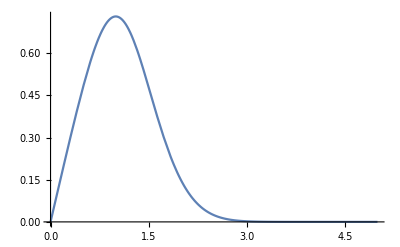

```mathematica
Plot[RPsiMinusSolutionM1[Tf[t,r],Rf[r]]/.TRule/.t->0/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.s->5/.ds->1/.A->1/.B->1,{r,0,5}]
```

we rewrite it in order to make it easier to use in the numerical code

```mathematica
(A B (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]])/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))/.Rf[r]-Tf[t,r]->J/.-Rf[r]+Tf[t,r]->-J/.ⅇ^(4 ds^2 Rf[r] Tf[t,r])->K/.(Rf[r]+Tf[t,r])->L
```

(A B (L+K (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]])/(Rf[r] (A B (J K+L)+2 ⅇ^(ds^2 L^2) Rf[r]))

```mathematica
(A B (L+K (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]])/(Rf[r] (A B (J K+L)+2 ⅇ^(ds^2 L^2) Rf[r]))/. 2 ds Rf[r]-2 ds Tf[t,r]->2dsJ
```

(A B (L+K ((-1+2 dsJ) (1+2 dsJ) Rf[r]-Tf[t,r])) χ[Rf[r]])/(Rf[r] (A B (J K+L)+2 ⅇ^(ds^2 L^2) Rf[r]))

Rescaled PsiPlus initial data for model 1

```mathematica
RRPsiPlusSolutionM1[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

(A B (-ⅇ^(ds^2 (r-2 Rf[r])^2) r+ⅇ^(ds^2 r^2) (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))

```mathematica
(A B (-ⅇ^(ds^2 (r-2 Rf[r])^2) r+ⅇ^(ds^2 r^2) (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))/.ⅇ^(ds^2 (r-2 Rf[r])^2)->K/.ⅇ^(ds^2 r^2)->J/.ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2))->J*K
```

(A B (-K r+J (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(Rf[r] (A B (K r-J (r-2 Rf[r]))+2 J K Rf[r]))

We collect the K coefficient, since it could give divergences during the computational implementation

```mathematica
Collect[A B (-K r+J (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2,K]
Collect[Rf[r] (A B (K r-J (r-2 Rf[r]))+2 J K Rf[r]),K]
```

-A B K r χ[Rf[r]]^2+A B J (r-4 ds^2 (r-2 Rf[r])^2 Rf[r]) χ[Rf[r]]^2

-A B J (r-2 Rf[r]) Rf[r]+K Rf[r] (A B r+2 J Rf[r])

The equation become

```mathematica
(-A B  r χ[Rf[r]]^2+A B J K^-1 (r-4 ds^2 (r-2 Rf[r])^2 Rf[r]) χ[Rf[r]]^2)/(-A B J K^-1 (r-2 Rf[r]) Rf[r]+Rf[r] (A B r+2 J Rf[r]))
```

(-A B r χ[Rf[r]]^2+(A B J (r-4 ds^2 (r-2 Rf[r])^2 Rf[r]) χ[Rf[r]]^2)/K)/(-(A B J (r-2 Rf[r]) Rf[r])/K+Rf[r] (A B r+2 J Rf[r]))

when r ->s:

```mathematica
(A B (-ⅇ^(ds^2 (r-2 Rf[r])^2) r) χ[Rf[r]]^2)/(2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]^2)//FullSimplify
```

-(A B ⅇ^(-ds^2 r^2) r χ[Rf[r]]^2)/(2 Rf[r]^2)

Hence RRPsiPlus goes to zero when r->s

Then when r->0:

```mathematica
(A B (-ⅇ^(ds^2 (r-2 Rf[r])^2) r+ⅇ^(ds^2 r^2) (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))/.r->0
```

-(16 A B ds^2 Rf[0]^2 χ[Rf[0]]^2)/(2 A B Rf[0]+2 ⅇ^(4 ds^2 Rf[0]^2) Rf[0])

RPsiPlus goes to  when r->0

Rescaled PsiMinus initial data for model 1

```mathematica
RPsiMinusSolutionM1[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

(A B (-ⅇ^(ds^2 r^2) (r-2 Rf[r])+ⅇ^(ds^2 (r-2 Rf[r])^2) (r+(-2+4 ds^2 r^2) Rf[r])) χ[Rf[r]])/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))

```mathematica
(A B (-ⅇ^(ds^2 r^2) (r-2 Rf[r])+ⅇ^(ds^2 (r-2 Rf[r])^2) (r+(-2+4 ds^2 r^2) Rf[r])) χ[Rf[r]])/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))/.ⅇ^(ds^2 (r-2 Rf[r])^2)->K/.ⅇ^(ds^2 r^2)->J/.ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2))->J*K
```

(A B (-J (r-2 Rf[r])+K (r+(-2+4 ds^2 r^2) Rf[r])) χ[Rf[r]])/(Rf[r] (A B (K r-J (r-2 Rf[r]))+2 J K Rf[r]))

We collect the K coefficients:

```mathematica
Collect[A B (-J (r-2 Rf[r])+K (r+(-2+4 ds^2 r^2) Rf[r])) χ[Rf[r]],K]
Collect[Rf[r] (A B (K r-J (r-2 Rf[r]))+2 J K Rf[r]),K]
```

-A B J (r-2 Rf[r]) χ[Rf[r]]+A B K (r+(-2+4 ds^2 r^2) Rf[r]) χ[Rf[r]]

-A B J (r-2 Rf[r]) Rf[r]+K Rf[r] (A B r+2 J Rf[r])

So we obtain

```mathematica
(-A B J K^-1 (r-2 Rf[r]) χ[Rf[r]]+A B K(r+(-2+4 ds^2 r^2) Rf[r]) χ[Rf[r]])/(-A B J K^-1(r-2 Rf[r]) Rf[r]+ Rf[r] (A B r+2 J Rf[r]))
```

(-(A B J (r-2 Rf[r]) χ[Rf[r]])/K+A B K (r+(-2+4 ds^2 r^2) Rf[r]) χ[Rf[r]])/(-(A B J (r-2 Rf[r]) Rf[r])/K+Rf[r] (A B r+2 J Rf[r]))

In the limit r->s

```mathematica
(A B (ⅇ^(ds^2 (r-2 Rf[r])^2) (r+(-2+4 ds^2 r^2) Rf[r])))/(2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r])//FullSimplify
```

(A B ⅇ^(-ds^2 r^2) (r+(-2+4 ds^2 r^2) Rf[r]))/(2 Rf[r])

hacking is so fun

```mathematica
Drop[{Derivative[1,0][Rψ][t,r], Derivative[1,0][SubPlus[R.b2ψ]][t,r],Derivative[1,0][SubMinus[Rψ]][t,r]}/.GoodRescaledEquationsHypSlices,1];
Collect[%,{Derivative[0,1][SubPlus[R.b2ψ]][t,r],Derivative[0,1][SubMinus[Rψ]][t,r],SubPlus[R.b2ψ][t,r],SubMinus[Rψ][t,r]},Simplify]
```

{}

## Initial conditions for the rescaled hyperboloidal model 3 equation with characteristic variables

```mathematica
Psi1SolutionM3 = Function[{x,z},C1*Sin[Log[1+Solution[x,z]]/C1]]
```

Function[{x,z},C1 Sin[Log[1+Solution[x,z]]/C1]]

```mathematica
Psi2SolutionM3 = Function[{x,z},C2*Cos[Log[1+Solution[x,z]]/C2]]
```

Function[{x,z},C2 Cos[Log[1+Solution[x,z]]/C2]]

```mathematica
Psi1SolutionM3[Tf[t,r],Rf[r]]/.Tf[t,r]->0
```

C1 Sin[Log[1+A ⅇ^(-ds^2 Rf[r]^2)]/C1]

```mathematica
Psi2SolutionM3[Tf[t,r],Rf[r]]/.Tf[t,r]->0
```

C2 Cos[Log[1+A ⅇ^(-ds^2 Rf[r]^2)]/C2]

```mathematica
Psi1SolutionPrimeM3 =Function[{x,z},D[Psi1SolutionM3[x,z],z]]
Psi2SolutionPrimeM3 =Function[{x,z},D[Psi2SolutionM3[x,z],z]]
```

Function[{x,z},∂_z Psi1SolutionM3[x,z]]

Function[{x,z},∂_z Psi2SolutionM3[x,z]]

```mathematica
Psi1SolutionDotM3 =Function[{x,z},D[Psi1SolutionM3[x,z],x]]
Psi2SolutionDotM3 =Function[{x,z},D[Psi2SolutionM3[x,z],x]]
```

Function[{x,z},∂_x Psi1SolutionM3[x,z]]

Function[{x,z},∂_x Psi2SolutionM3[x,z]]

```mathematica
Psi1PlusSolutionM3 = Function[{x,z},Psi1SolutionDotM3[x,z]+Psi1SolutionPrimeM3[x,z]]
Psi1MinusSolutionM3= Function[{x,z},Psi1SolutionDotM3[x,z]-Psi1SolutionPrimeM3[x,z]]
```

Function[{x,z},Psi1SolutionDotM3[x,z]+Psi1SolutionPrimeM3[x,z]]

Function[{x,z},Psi1SolutionDotM3[x,z]-Psi1SolutionPrimeM3[x,z]]

```mathematica
Psi1PlusSolutionM3[Tf[t,r],Rf[r]]//FullSimplify
```

-((A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) Cos[Log[1+(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]))/(2 Rf[r])]/C1] (ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]+Rf[r] (-1+4 ds^2 (Rf[r]+Tf[t,r])^2)))/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]))))

```mathematica
Psi1MinusSolutionM3[Tf[t,r],Rf[r]]//FullSimplify
```

(A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) Cos[Log[1+(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]))/(2 Rf[r])]/C1] (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))))/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

```mathematica
Psi2PlusSolutionM3 = Function[{x,z},Psi2SolutionDotM3[x,z]+Psi2SolutionPrimeM3[x,z]]
Psi2MinusSolutionM3= Function[{x,z},Psi2SolutionDotM3[x,z]-Psi2SolutionPrimeM3[x,z]]
```

Function[{x,z},Psi2SolutionDotM3[x,z]+Psi2SolutionPrimeM3[x,z]]

Function[{x,z},Psi2SolutionDotM3[x,z]-Psi2SolutionPrimeM3[x,z]]

```mathematica
Psi2PlusSolutionM3[Tf[t,r],Rf[r]]//FullSimplify
```

(A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) Sin[Log[1+(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]))/(2 Rf[r])]/C2] (ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]+Rf[r] (-1+4 ds^2 (Rf[r]+Tf[t,r])^2)))/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

We rescale the solution and apply the hyperboloidal compactification

```mathematica
RPsi1SolutionM3=Function[{x,z},Psi1SolutionM3[x,z]*χ[z]]
RPsi1SolutionM3[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},Psi1SolutionM3[x,z] χ[z]]

C1 Sin[Log[1+(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]))/(2 Rf[r])]/C1] χ[Rf[r]]

```mathematica
RPsi2SolutionM3=Function[{x,z},Psi2SolutionM3[x,z]*χ[z]]
RPsi2SolutionM3[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},Psi2SolutionM3[x,z] χ[z]]

C2 Cos[Log[1+(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]))/(2 Rf[r])]/C2] χ[Rf[r]]

Initial condition for Psi1:

```mathematica
RPsi1SolutionM3[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

C1 Sin[Log[1+(A ⅇ^(-ds^2 r^2) r-A ⅇ^(-ds^2 (r-2 Rf[r])^2) (r-2 Rf[r]))/(2 Rf[r])]/C1] χ[Rf[r]]

when r->s the equation becomes:

```mathematica
(A E^(-ds^2 r^2)*r)/2
```

1/2 A ⅇ^(-ds^2 r^2) r

when r->0 Psi1 goes to zero.

Initial condition for Psi2:

```mathematica
RPsi2SolutionM3[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

C2 Cos[Log[1+(A ⅇ^(-ds^2 r^2) r-A ⅇ^(-ds^2 (r-2 Rf[r])^2) (r-2 Rf[r]))/(2 Rf[r])]/C2] χ[Rf[r]]

```mathematica
RPsi2SolutionM3[Tf[t,r],Rf[r]]/.TRule/.t->0/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.s->5/.ds->1/.A->1/.C2->1
```

√(1+r^2/((1-r^2/25)^2)) Cos[Log[1+((1-r^2/25) (ⅇ^(-r^2) r+ⅇ^(-(-r+(2 r)/(1-r^2/25))^2) (-r+(2 r)/(1-r^2/25))))/(2 r)]]

We now look at the rescaled compactified solutions for the PsiPlus’ and PsiMinus’

PsiOnePlus solution:

```mathematica
RRPsi1PlusSolutionM3= Function[{x,z},Psi1PlusSolutionM3[x,z]*χ[z]^2]
RRPsi1PlusSolutionM3[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},Psi1PlusSolutionM3[x,z] χ[z]^2]

-((A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) Cos[Log[1+(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]))/(2 Rf[r])]/C1] (ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]+Rf[r] (-1+4 ds^2 (Rf[r]+Tf[t,r])^2)) χ[Rf[r]]^2)/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]))))

we rewrite rewrite the solution or computational aims introducing some coefficients

```mathematica
-((A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]+Rf[r] (-1+4 ds^2 (Rf[r]+Tf[t,r])^2)) χ[Rf[r]]^2 sen'[Log[1+(B (A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])))/(2 Rf[r])]/C])/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]))))/.Rf[r]-Tf[t,r]->J/.-Rf[r]+Tf[t,r]->-J/.ⅇ^(4 ds^2 Rf[r] Tf[t,r])->K/.(Rf[r]+Tf[t,r])->L/.Rf[r]^2+Tf[t,r]^2->M/.(B (A ⅇ^(-ds^2 J^2) J+A ⅇ^(-ds^2 L^2) L))/(2 Rf[r])->N/.Log[1+N]/C1->P
```

-(A B ⅇ^(ds^2 J^2) (J K+(-1+4 ds^2 L^2) Rf[r]+Tf[t,r]) χ[Rf[r]]^2 sen'[Log[1+N]/C])/(Rf[r] (A B ⅇ^(ds^2 J^2) (J K+L)+2 ⅇ^(2 ds^2 M) Rf[r]))

```mathematica
RRPsi2PlusSolutionM3= Function[{x,z},Psi2PlusSolutionM3[x,z]*χ[z]^2]
RRPsi2PlusSolutionM3[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},Psi2PlusSolutionM3[x,z] χ[z]^2]

(A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) Sin[Log[1+(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]))/(2 Rf[r])]/C2] (ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]+Rf[r] (-1+4 ds^2 (Rf[r]+Tf[t,r])^2)) χ[Rf[r]]^2)/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

```mathematica
-((A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]+Rf[r] (-1+4 ds^2 (Rf[r]+Tf[t,r])^2)) χ[Rf[r]]^2 sen'[Log[1+(B (A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])))/(2 Rf[r])]/C1])/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]))))
```

-((A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]+Rf[r] (-1+4 ds^2 (Rf[r]+Tf[t,r])^2)) χ[Rf[r]]^2 sen'[Log[1+(B (A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])))/(2 Rf[r])]/C1])/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]))))

we introduce some coefficients

```mathematica
-((A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]+Rf[r] (-1+4 ds^2 (Rf[r]+Tf[t,r])^2)) χ[Rf[r]]^2 sen'[Log[1+(B (A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])))/(2 Rf[r])]/C2])/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]))))/.Rf[r]-Tf[t,r]->J/.-Rf[r]+Tf[t,r]->-J/.ⅇ^(4 ds^2 Rf[r] Tf[t,r])->K/.(Rf[r]+Tf[t,r])->L/.Rf[r]^2+Tf[t,r]^2->M/.(B (A ⅇ^(-ds^2 J^2) J+A ⅇ^(-ds^2 L^2) L))/(2 Rf[r])->N/.Log[1+N]/C2->P
```

-(A B ⅇ^(ds^2 J^2) (J K+(-1+4 ds^2 L^2) Rf[r]+Tf[t,r]) χ[Rf[r]]^2 sen'[P])/(Rf[r] (A B ⅇ^(ds^2 J^2) (J K+L)+2 ⅇ^(2 ds^2 M) Rf[r]))

Psi1Minus exact solution:

```mathematica
RPsi1MinusSolutionM3 = Function[{x,z},Psi1MinusSolutionM3[x,z]*χ[z]]
RPsi1MinusSolutionM3[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},Psi1MinusSolutionM3[x,z] χ[z]]

(A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) Cos[Log[1+(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]))/(2 Rf[r])]/C1] (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]])/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

we introduce some coefficients

```mathematica
(A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]] sen'[Log[1+(B (A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])))/(2 Rf[r])]/C1])/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))/. 2 ds Rf[r]-2 ds Tf[t,r]->2ds(Rf[r]-Tf[t,r])/.Rf[r]-Tf[t,r]->J/.-Rf[r]+Tf[t,r]->-J/.ⅇ^(4 ds^2 Rf[r] Tf[t,r])->K/.(Rf[r]+Tf[t,r])->L/.Rf[r]^2+Tf[t,r]^2->M/.(B (A ⅇ^(-ds^2 J^2) J+A ⅇ^(-ds^2 L^2) L))/(2 Rf[r])->N/.Log[1+N]/C1->P
```

(A B ⅇ^(ds^2 J^2) (L+K ((-1+2 ds J) (1+2 ds J) Rf[r]-Tf[t,r])) χ[Rf[r]] sen'[P])/(Rf[r] (A B ⅇ^(ds^2 J^2) (J K+L)+2 ⅇ^(2 ds^2 M) Rf[r]))

```mathematica
RPsi2MinusSolutionM3 = Function[{x,z},Psi2MinusSolutionM3[x,z]*χ[z]]
RPsi2MinusSolutionM3[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},Psi2MinusSolutionM3[x,z] χ[z]]

-((A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) Sin[Log[1+(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]))/(2 Rf[r])]/C2] (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]])/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]))))

we introduce some coefficients:

```mathematica
(A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]] cos'[Log[1+(B (A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])))/(2 Rf[r])]/C2])/(Rf[r] (2 ⅇ^(2 ds^2 (Rf[r]^2+Tf[t,r]^2)) Rf[r]+A B ⅇ^(ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))/. 2 ds Rf[r]-2 ds Tf[t,r]->2ds(Rf[r]-Tf[t,r])/.Rf[r]-Tf[t,r]->J/.-Rf[r]+Tf[t,r]->-J/.ⅇ^(4 ds^2 Rf[r] Tf[t,r])->K/.(Rf[r]+Tf[t,r])->L/.Rf[r]^2+Tf[t,r]^2->M/.(B (A ⅇ^(-ds^2 J^2) J+A ⅇ^(-ds^2 L^2) L))/(2 Rf[r])->N/.Log[1+N]/C2->P
```

(A B ⅇ^(ds^2 J^2) (L+K ((-1+2 ds J) (1+2 ds J) Rf[r]-Tf[t,r])) χ[Rf[r]] cos'[P])/(Rf[r] (A B ⅇ^(ds^2 J^2) (J K+L)+2 ⅇ^(2 ds^2 M) Rf[r]))

INITIAL DATA

Rescaled Psi1Plus initial data for model 3

```mathematica
RRPsi1PlusSolutionM3[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

-(A Cos[Log[1+(A ⅇ^(-ds^2 r^2) r-A ⅇ^(-ds^2 (r-2 Rf[r])^2) (r-2 Rf[r]))/(2 Rf[r])]/C1] (ⅇ^(ds^2 (r-2 Rf[r])^2) r+ⅇ^(ds^2 r^2) (-r+4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(Rf[r] (A (-ⅇ^(ds^2 r^2)+ⅇ^(ds^2 (r-2 Rf[r])^2)) r+2 (A ⅇ^(ds^2 r^2)+ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2))) Rf[r]))

```mathematica
-(A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r+ⅇ^(ds^2 r^2) (-r+4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2 sen'[Log[1+(B (A ⅇ^(-ds^2 r^2) r-A ⅇ^(-ds^2 (r-2 Rf[r])^2) (r-2 Rf[r])))/(2 Rf[r])]/C1])/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))/.ⅇ^(ds^2 (r-2 Rf[r])^2)->K/.ⅇ^(-ds^2 (r-2 Rf[r])^2)->1/K/.ⅇ^(ds^2 r^2)->J/.ⅇ^(-ds^2 r^2)->1/J/.ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2))->J*K/.r-2 Rf[r]->L
```

-(A B (K r+J (-r+4 ds^2 L^2 Rf[r])) χ[Rf[r]]^2 sen'[Log[1+(B (-(A L)/K+(A r)/J))/(2 Rf[r])]/C1])/(Rf[r] (A B (-J L+K r)+2 J K Rf[r]))

We collect the K coefficient, since it could give divergences during the computational implementation

```mathematica
Collect[A B (K r+J (-r+4 ds^2 L^2 Rf[r])) χ[Rf[r]]^2 sen'[Log[1+(B (-(A L)/K+(A r)/J))/(2 Rf[r])]/C1],K]
Collect[Rf[r] (A B (-J L+K r)+2 J K Rf[r]),K]
```

A B K r χ[Rf[r]]^2 sen'[Log[1+(B (-(A L)/K+(A r)/J))/(2 Rf[r])]/C1]+A B J (-r+4 ds^2 L^2 Rf[r]) χ[Rf[r]]^2 sen'[Log[1+(B (-(A L)/K+(A r)/J))/(2 Rf[r])]/C1]

-A B J L Rf[r]+K Rf[r] (A B r+2 J Rf[r])

The equation become

```mathematica
(A B  r χ[Rf[r]]^2 sen'[Log[1+(B (-(A L)/K+(A r)/J))/(2 Rf[r])]/C1]+K^-1 A B J (-r+4 ds^2 L^2 Rf[r]) χ[Rf[r]]^2 sen'[Log[1+(B (-(A L)/K+(A r)/J))/(2 Rf[r])]/C1])/(-A B J L Rf[r] K^-1+ Rf[r] (A B r+2 J Rf[r]))
```

(A B r χ[Rf[r]]^2 sen'[Log[1+(B (-(A L)/K+(A r)/J))/(2 Rf[r])]/C1]+(A B J (-r+4 ds^2 L^2 Rf[r]) χ[Rf[r]]^2 sen'[Log[1+(B (-(A L)/K+(A r)/J))/(2 Rf[r])]/C1])/K)/(-(A B J L Rf[r])/K+Rf[r] (A B r+2 J Rf[r]))

when r->s